```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["ErrorBarPlots`"];
```

## BW fit

### Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fit[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=10 temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];(*maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,0,1/2(maxx-minx),1/20}],First][[All,2]]]];*)
maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,Length[Tscan]}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];];
```

```mathematica
fitONE[input_]:=Module[{maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxis,mins,hwhmi,bad},
maxx=Max[input[[All,1]]];
minx=Min[input[[All,1]]];
maxy=Max[input[[All,2]]];
maxyx=input[[Position[input,Max[input[[All,2]]]][[1,1]],1]];
maxyi=Position[input[[All,1]],maxyx][[1,1]];
maxxy=input[[Position[input,Max[input[[All,1]]]][[1,1]],2]];
inter=Interpolation[input,InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,1,1/2(maxx-minx),1/20}],First][[All,2]]]];bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[[All,1]],Nearest[input[[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[[maxxis[[i]]-30,2]]>input[[maxxis[[i]],2]],input[[maxxis[[i]]+30,2]]>input[[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[[All,2]],Min[input[[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input]]];,
hwhmi=Position[input,Nearest[input[[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input],maxyi+3(maxyi-hwhmi),Length[input]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input,Nearest[input[[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];];
```

### Fitting

```mathematica
uscanI={1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1};
uscanI1={1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10};
uscan={1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,99/100};
uscan1={1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10};
```

#### Charmonium Tc Parallel

```mathematica
Do[ccdata[n]=Import["cc/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectra.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[ccdatau[n]=Import["cc/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectrau.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[ccdatal[n]=Import["cc/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectral.dat"];,{n,Length[uscan]}];
```

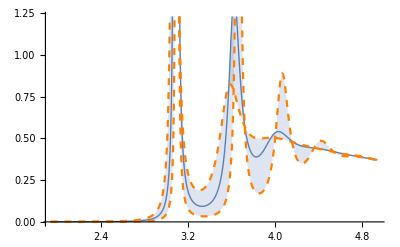

```mathematica
Block[{n=10},ListPlot[{ccdata[n],ccdatal[n],ccdatau[n]},Joined->True,Filling->{1->{2},1->{3}},PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata,ccmodel,uscanI]];
Quiet[fit[ccdatal,ccmodell,uscanI]];
Quiet[fit[ccdatau,ccmodelu,uscanI]];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[wr,wrfitccl,ccmodell];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitcc,ccmodel];
store[Γ,gfitccl,ccmodell];
store[Γ,gfitccu,ccmodelu];
store[const,cfitcc,ccmodel];
store[const,cfitccl,ccmodell];
store[const,cfitccu,ccmodelu];
store[δbg,dfitcc,ccmodel];
store[δbg,dfitccl,ccmodell];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitcc,ccmodel];
store[shift,sfitccl,ccmodell];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitcc,ccmodel];
store[shift2,s2fitccl,ccmodell];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitcc,ccmodel];
storearea[areafitccl,ccmodell];
storearea[areafitccu,ccmodelu];
```

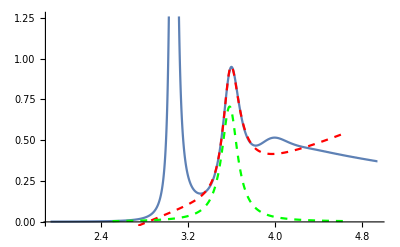

```mathematica
Block[{i=1,ii=2},Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

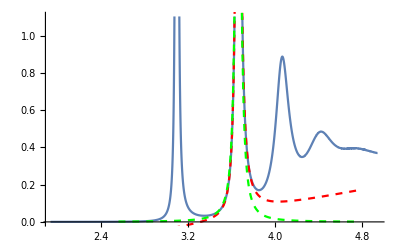

```mathematica
Block[{i=10,ii=2},Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

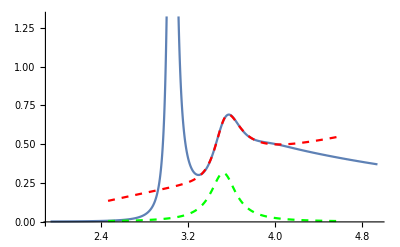

```mathematica
Block[{i=7,ii=2},Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
Transpose[{uscan,wrfitcc[[All,1]],wrfitccu[[All,1]],wrfitccl[[All,1]]}]
```

{{1/10,3.06637,3.03909,3.08597},{1/5,3.06681,3.03972,3.08621},{3/10,3.06755,3.0408,3.08661},{2/5,3.06865,3.04238,3.0872},{1/2,3.07014,3.04457,3.088},{3/5,3.07212,3.04752,3.08903},{7/10,3.07472,3.05147,3.09037},{4/5,3.07816,3.05683,3.0921},{9/10,3.08284,3.06432,3.09436},{99/100,3.08789,3.07263,3.09665}}

```mathematica
wrfitcc1={{1/10,3.0663689453922336,3.0390934656531807,3.0859692271996244},{1/5,3.0668058473417936,3.0397189900325867,3.0862075210146163},{3/10,3.067553741431351,3.0407966528799637,3.0866133652423136},{2/5,3.0686467685604537,3.0423830812866726,3.08720153774853},{1/2,3.070138878635057,3.044574243254233,3.0879956588139197},{3/5,3.07211585767268,3.0475203363172256,3.089032572045881},{7/10,3.074715021207178,3.051466039196709,3.0903697028304995},{4/5,3.0781636158116403,3.0568255778981985,3.092099855706263},{9/10,3.0828419814504264,3.0643190101985134,3.094364697696784},{99/100,3.0878877753430474,3.0726269872021166,3.0966521743257807}};
```

```mathematica
wrfitcc1inter=Interpolation[wrfitcc1[[All,;;2]],InterpolationOrder->1];
wrfitcc1interl=Interpolation[wrfitcc1[[All,1;;3;;2]],InterpolationOrder->1];
wrfitcc1interu=Interpolation[wrfitcc1[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,wrfitcc1inter[0],wrfitcc1interl[0],wrfitcc1interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,3.06593,3.03847,3.08573}

```mathematica
Export["final/Jpsi_mass_T150_par.dat",Join[{{0,wrfitcc1inter[0],wrfitcc1interl[0],wrfitcc1interu[0]}},wrfitcc1]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Jpsi_mass_T150_par.dat

```mathematica
Transpose[{uscan,wrfitcc[[All,2]],wrfitccu[[All,2]],wrfitccl[[All,2]]}]
```

{{1/10,3.58138,3.50479,3.64311},{1/5,3.58193,3.50523,3.64344},{3/10,3.58348,3.50659,3.64401},{2/5,3.58467,3.50861,3.64486},{1/2,3.58697,3.51158,3.64602},{3/5,3.59021,3.51607,3.64759},{7/10,3.59489,3.52306,3.64967},{4/5,3.60088,3.53321,3.65248},{9/10,3.60973,3.54906,3.65628},{99/100,3.61817,3.56043,3.65978}}

```mathematica
wrfitcc2={{1/10,3.5813775407158297,3.5047947648818103,3.6431094799172543},{1/5,3.5819343458071082,3.5052295758486096,3.643440357700103},{3/10,3.5834798258904614,3.5065897060179534,3.644013145006523},{2/5,3.584665296790009,3.5086139627615878,3.6448562527619366},{1/2,3.586967002758437,3.51157760358517,3.6460228958882888},{3/5,3.5902108415435894,3.5160670342632545,3.6475910324616403},{7/10,3.5948912045016255,3.5230573616818277,3.649673992214731},{4/5,3.6008818600571852,3.5332122262867602,3.65247795733201},{9/10,3.609731951966939,3.549055257458368,3.656281199189587},{99/100,3.618172131285003,3.5604329339917355,3.659776357492796}};
```

```mathematica
wrfitcc2inter=Interpolation[wrfitcc2[[All,;;2]],InterpolationOrder->1];
wrfitcc2interl=Interpolation[wrfitcc2[[All,1;;3;;2]],InterpolationOrder->1];
wrfitcc2interu=Interpolation[wrfitcc2[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,wrfitcc2inter[0],wrfitcc2interl[0],wrfitcc2interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,3.58082,3.50436,3.64278}

```mathematica
Export["final/psip_mass_T150_par.dat",Join[{{0,wrfitcc2inter[0],wrfitcc2interl[0],wrfitcc2interu[0]}},wrfitcc2]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/psip_mass_T150_par.dat

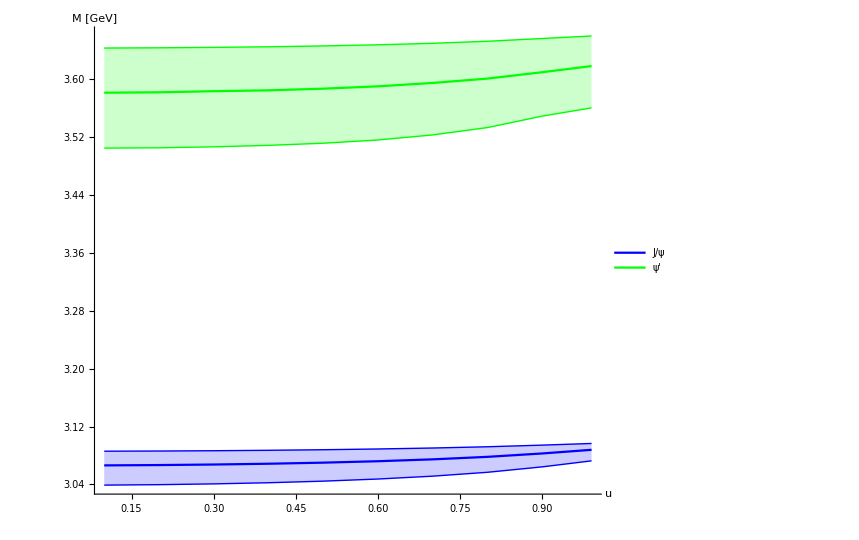

```mathematica
ListPlot[{Transpose[{uscan[[;;]],wrfitcc1[[;;,2]]}],Transpose[{uscan[[;;]],wrfitcc1[[;;,3]]}],Transpose[{uscan[[;;]],wrfitcc1[[;;,4]]}],Transpose[{uscan[[;;]],wrfitcc2[[;;,2]]}],Transpose[{uscan[[;;]],wrfitcc2[[;;,3]]}],Transpose[{uscan[[;;]],wrfitcc2[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.8,0.4}]]
```

```mathematica
Transpose[{uscan,gfitcc[[All,1]],gfitccu[[All,1]],gfitccl[[All,1]]}]
```

{{1/10,0.0350962,0.0574362,0.0156346},{1/5,0.0351578,0.0576631,0.0156238},{3/10,0.0352459,0.058021,0.0155985},{2/5,0.0353337,0.0584792,0.015544},{1/2,0.0353729,0.0589657,0.015437},{3/5,0.0352718,0.0593501,0.0152328},{7/10,0.0348486,0.059353,0.0148476},{4/5,0.0336791,0.0582929,0.0140898},{9/10,0.0304404,0.053974,0.012385},{99/100,0.0169017,0.0319523,0.0063985}}

```mathematica
gfitcc1={{1/10,0.03509623614433616,0.05743619681659198,0.015634603134638082},{1/5,0.03515775412941795,0.057663126758552674,0.015623773826675964},{3/10,0.03524592325311088,0.05802096543426276,0.015598487673072769},{2/5,0.03533374179543238,0.05847919069792092,0.015544007120240158},{1/2,0.03537285730864292,0.058965720435645734,0.015437037413929038},{3/5,0.03527177743217072,0.0593500963489929,0.015232824038684643},{7/10,0.03484858267752482,0.05935303798752198,0.014847644044053806},{4/5,0.03367905357788095,0.05829293395886445,0.014089849157962955},{9/10,0.030440403835104164,0.0539740069035063,0.012385039037227874},{99/100,0.01690172487365056,0.03195231759866381,0.006398496551710401}};
```

```mathematica
gfitcc1inter=Interpolation[gfitcc1[[All,;;2]],InterpolationOrder->1];
gfitcc1interl=Interpolation[gfitcc1[[All,1;;3;;2]],InterpolationOrder->1];
gfitcc1interu=Interpolation[gfitcc1[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitcc1inter[0],gfitcc1interl[0],gfitcc1interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.0350347,0.0572093,0.0156454}

```mathematica
gfitcc1n=Join[{{0,0.035034718159254366,0.05720926687463129,0.0156454324426002}},gfitcc1]
```

{{0,0.0350347,0.0572093,0.0156454},{1/10,0.0350962,0.0574362,0.0156346},{1/5,0.0351578,0.0576631,0.0156238},{3/10,0.0352459,0.058021,0.0155985},{2/5,0.0353337,0.0584792,0.015544},{1/2,0.0353729,0.0589657,0.015437},{3/5,0.0352718,0.0593501,0.0152328},{7/10,0.0348486,0.059353,0.0148476},{4/5,0.0336791,0.0582929,0.0140898},{9/10,0.0304404,0.053974,0.012385},{99/100,0.0169017,0.0319523,0.0063985}}

```mathematica
gfitcc1inter=Interpolation[gfitcc1n[[All,;;2]],InterpolationOrder->5];
gfitcc1interl=Interpolation[gfitcc1n[[All,1;;3;;2]],InterpolationOrder->5];
gfitcc1interu=Interpolation[gfitcc1n[[All,1;;4;;3]],InterpolationOrder->5];
```

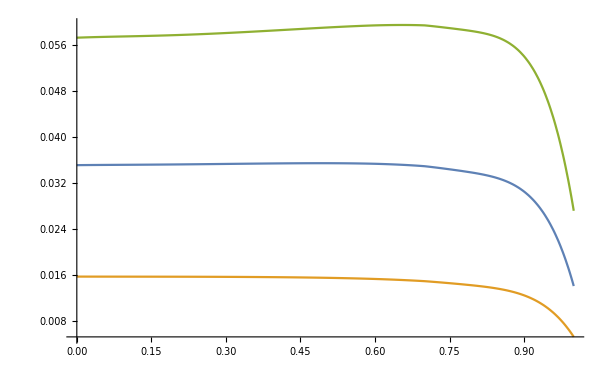

```mathematica
Plot[{gfitcc1inter[x],gfitcc1interu[x],gfitcc1interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/Jpsi_width_T150_par.dat",Table[{u,gfitcc1inter[u],gfitcc1interu[u],gfitcc1interl[u]},{u,0,1,1/20}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Jpsi_width_T150_par.dat

```mathematica
Transpose[{uscan,gfitcc[[All,2]],gfitccu[[All,2]],gfitccl[[All,2]]}]
```

{{1/10,0.176253,0.248834,0.0934501},{1/5,0.177102,0.250883,0.0936502},{3/10,0.178397,0.254801,0.0939326},{2/5,0.180679,0.259861,0.0942564},{1/2,0.182799,0.265861,0.0944707},{3/5,0.185277,0.273122,0.0943689},{7/10,0.187057,0.27982,0.0935104},{4/5,0.186475,0.285328,0.0907741},{9/10,0.178167,0.280874,0.0827284},{99/100,0.120935,0.205619,0.0469587}}

```mathematica
gfitcc2={{1/10,0.17625321159126014,0.24883366467103013,0.09345008068864988},{1/5,0.17710245174984104,0.25088338350745293,0.09365015485532839},{3/10,0.1783970370174799,0.2548014129315289,0.09393257959213677},{2/5,0.1806791359674714,0.25986100158180736,0.09425635323046107},{1/2,0.1827994237453654,0.2658606600650281,0.09447073853344325},{3/5,0.1852766065287437,0.2731221067163092,0.09436891611205724},{7/10,0.18705652960803082,0.27982048781387053,0.09351042268216267},{4/5,0.18647466551533431,0.2853277181357263,0.09077407251580498},{9/10,0.17816665360374812,0.2808738740156078,0.08272837597957543},{99/100,0.1209353789598855,0.20561862850401713,0.046958743492029734}};
```

```mathematica
gfitcc2inter=Interpolation[gfitcc2[[All,;;2]],InterpolationOrder->1];
gfitcc2interl=Interpolation[gfitcc2[[All,1;;3;;2]],InterpolationOrder->1];
gfitcc2interu=Interpolation[gfitcc2[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitcc2inter[0],gfitcc2interl[0],gfitcc2interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.175404,0.246784,0.09325}

```mathematica
gfitcc2n=Join[{{0,0.17540397143267925,0.24678394583460733,0.09325000652197137}},gfitcc2]
```

{{0,0.175404,0.246784,0.09325},{1/10,0.176253,0.248834,0.0934501},{1/5,0.177102,0.250883,0.0936502},{3/10,0.178397,0.254801,0.0939326},{2/5,0.180679,0.259861,0.0942564},{1/2,0.182799,0.265861,0.0944707},{3/5,0.185277,0.273122,0.0943689},{7/10,0.187057,0.27982,0.0935104},{4/5,0.186475,0.285328,0.0907741},{9/10,0.178167,0.280874,0.0827284},{99/100,0.120935,0.205619,0.0469587}}

```mathematica
gfitcc2inter=Interpolation[gfitcc2n[[All,;;2]],InterpolationOrder->5];
gfitcc2interl=Interpolation[gfitcc2n[[All,1;;3;;2]],InterpolationOrder->5];
gfitcc2interu=Interpolation[gfitcc2n[[All,1;;4;;3]],InterpolationOrder->5];
```

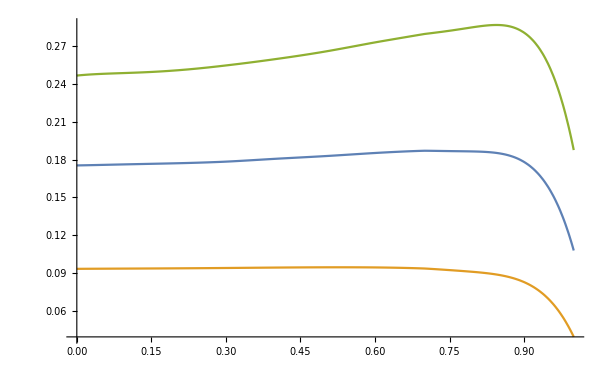

```mathematica
Plot[{gfitcc2inter[x],gfitcc2interu[x],gfitcc2interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/psip_width_T150_par.dat",Table[{u,gfitcc2inter[u],gfitcc2interu[u],gfitcc2interl[u]},{u,0,1,1/20}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/psip_width_T150_par.dat

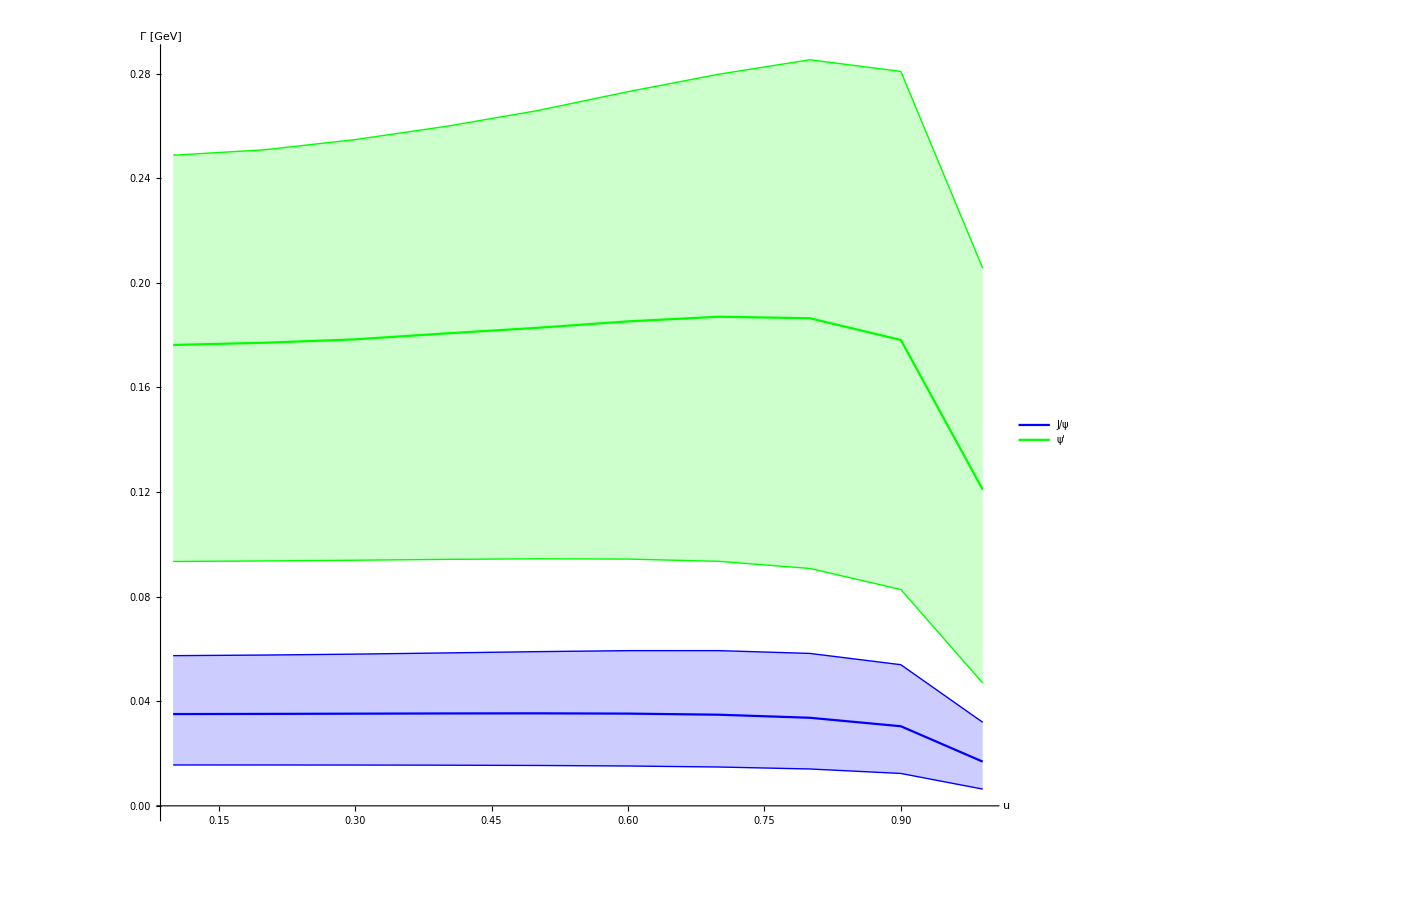

```mathematica
ListPlot[{Transpose[{uscan[[;;]],gfitcc1[[;;,2]]}],Transpose[{uscan[[;;]],gfitcc1[[;;,3]]}],Transpose[{uscan[[;;]],gfitcc1[[;;,4]]}],Transpose[{uscan[[;;]],gfitcc2[[;;,2]]}],Transpose[{uscan[[;;]],gfitcc2[[;;,3]]}],Transpose[{uscan[[;;]],gfitcc2[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.8,0.2}]]
```

#### Bottomonium Tc Parallel

```mathematica
Do[bbdata[n]=Import["bb/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectra.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[bbdatau[n]=Import["bb/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectrau.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[bbdatal[n]=Import["bb/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectral.dat"];,{n,Length[uscan]}];
```

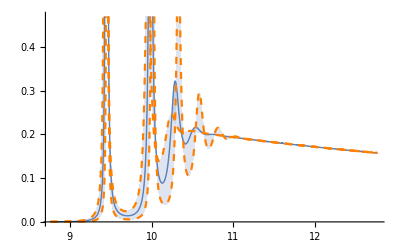

```mathematica
Block[{n=1},ListPlot[{bbdata[n],bbdatal[n],bbdatau[n]},Joined->True,Filling->{1->{2},1->{3}},PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[bbmodelu,bbmodell,bbmodel]
Quiet[fit[bbdata,bbmodel,uscanI]];
Quiet[fit[bbdatal,bbmodell,uscanI]];
Quiet[fit[bbdatau,bbmodelu,uscanI]];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[wr,wrfitbbl,bbmodell];
store[wr,wrfitbbu,bbmodelu];
store[Γ,gfitbb,bbmodel];
store[Γ,gfitbbl,bbmodell];
store[Γ,gfitbbu,bbmodelu];
store[const,cfitbb,bbmodel];
store[const,cfitbbl,bbmodell];
store[const,cfitbbu,bbmodelu];
store[δbg,dfitbb,bbmodel];
store[δbg,dfitbbl,bbmodell];
store[δbg,dfitbbu,bbmodelu];
store[shift,sfitbb,bbmodel];
store[shift,sfitbbl,bbmodell];
store[shift,sfitbbu,bbmodelu];
store[shift2,s2fitbb,bbmodel];
store[shift2,s2fitbbl,bbmodell];
store[shift2,s2fitbbu,bbmodelu];
storearea[areafitbb,bbmodel];
storearea[areafitbbl,bbmodell];
storearea[areafitbbu,bbmodelu];
```

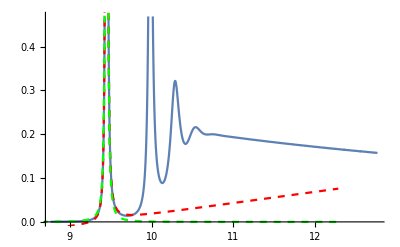

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[bbdata[i],Joined->True],Plot[BW[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],dfitbb[[i,ii]],cfitbb[[i,ii]],sfitbb[[i,ii]],s2fitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],cfitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

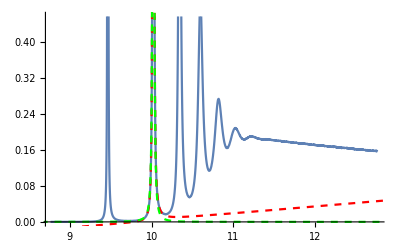

```mathematica
Block[{i=10,ii=2},Show[{ListPlot[bbdatal[i],Joined->True],Plot[BW[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],dfitbbl[[i,ii]],cfitbbl[[i,ii]],sfitbbl[[i,ii]],s2fitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],cfitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

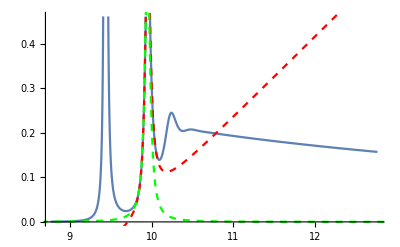

```mathematica
Block[{i=1,ii=2},Show[{ListPlot[bbdatau[i],Joined->True],Plot[BW[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],dfitbbu[[i,ii]],cfitbbu[[i,ii]],sfitbbu[[i,ii]],s2fitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],cfitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
Transpose[{uscan,wrfitbb[[All,1]],wrfitbbu[[All,1]],wrfitbbl[[All,1]]}]
```

{{1/10,9.4485,9.43744,9.45602},{1/5,9.44889,9.43801,9.45623},{3/10,9.44954,9.43898,9.45659},{2/5,9.45048,9.44037,9.4571},{1/2,9.45175,9.44226,9.45779},{3/5,9.45338,9.44471,9.45867},{7/10,9.45547,9.44786,9.45978},{4/5,9.45813,9.45192,9.46118},{9/10,9.46152,9.4572,9.46293},{99/100,9.46473,9.46248,9.46447}}

```mathematica
wrfitbb1={{1/10,9.44850057715624,9.437442205342954,9.456021104328052},{1/5,9.448885372754175,9.438009463361553,9.4562320298245},{3/10,9.449539216294518,9.438975102410682,9.456590008747193},{2/5,9.450482728817343,9.440372355044065,9.457103045662612},{1/2,9.451747836976256,9.442255098080404,9.457788951714488},{3/5,9.453384979917223,9.444706476471465,9.458670802355794},{7/10,9.45547154065031,9.447857620450897,9.459783729359778},{4/5,9.458127110183097,9.451916273261297,9.461181896302797},{9/10,9.461519428047483,9.457199599937889,9.462929535512176},{99/100,9.464727582919405,9.462476117840772,9.464469772234226}};
```

```mathematica
wrfitbb1inter=Interpolation[wrfitbb1[[All,;;2]],InterpolationOrder->1];
wrfitbb1interl=Interpolation[wrfitbb1[[All,1;;3;;2]],InterpolationOrder->1];
wrfitbb1interu=Interpolation[wrfitbb1[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
Export["final/Upsilon1_mass_T150_par.dat",Join[{{0,wrfitbb1inter[0],wrfitbb1interl[0],wrfitbb1interu[0]}},wrfitbb1]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Upsilon1_mass_T150_par.dat

```mathematica
Transpose[{uscan,wrfitbb[[All,2]],wrfitbbu[[All,2]],wrfitbbl[[All,2]]}]
```

{{1/10,9.98422,9.95023,10.009},{1/5,9.98468,9.95085,10.0093},{3/10,9.98546,9.952,10.0097},{2/5,9.98661,9.95362,10.0103},{1/2,9.98819,9.95594,10.0112},{3/5,9.99031,9.95906,10.0123},{7/10,9.99311,9.96329,10.0137},{4/5,9.99689,9.96914,10.0156},{9/10,10.0021,9.9775,10.0181},{99/100,10.008,9.98705,10.0207}}

```mathematica
wrfitbb2={{1/10,9.98422111782614,9.950227436568388,10.009047482441527},{1/5,9.984676157667005,9.9508546053834,10.00929741279056},{3/10,9.985460442136203,9.951998895751876,10.0097235860625},{2/5,9.986611212664238,9.95361639823814,10.010343111268174},{1/2,9.988193366691299,9.955940530194441,10.011183432732665},{3/5,9.990305616852085,9.959057777875975,10.012286559591614},{7/10,9.993114540620038,9.963287426535535,10.013720741094188},{4/5,9.996892155218609,9.969135781889975,10.015594462656255},{9/10,10.002118270727061,9.977497647747285,10.018086648003711},{99/100,10.007996402701894,9.987050475979226,10.020710641277715}};
```

```mathematica
wrfitbb2inter=Interpolation[wrfitbb2[[All,;;2]],InterpolationOrder->1];
wrfitbb2interl=Interpolation[wrfitbb2[[All,1;;3;;2]],InterpolationOrder->1];
wrfitbb2interu=Interpolation[wrfitbb2[[All,1;;4;;3]],InterpolationOrder->1];
Export["final/Upsilon2_mass_T150_par.dat",Join[{{0,wrfitbb2inter[0],wrfitbb2interl[0],wrfitbb2interu[0]}},wrfitbb2]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Upsilon2_mass_T150_par.dat

```mathematica
Transpose[{uscan,wrfitbb[[All,3]],wrfitbbu[[All,3]],wrfitbbl[[All,3]]}]
```

{{1/10,10.2813,10.2155,10.327},{1/5,10.2781,10.2165,10.3273},{3/10,10.2789,10.2173,10.3278},{2/5,10.284,10.2196,10.3285},{1/2,10.2823,10.2233,10.3296},{3/5,10.285,10.2264,10.3309},{7/10,10.2885,10.2333,10.3328},{4/5,10.294,10.2414,10.3352},{9/10,10.3013,10.2529,10.3386},{99/100,10.3108,10.2652,10.3422}}

```mathematica
wrfitbb3={{1/10,10.281308712216072,10.215453229283725,10.326960165478548},{1/5,10.278062123229603,10.216453190925153,10.327250282007036},{3/10,10.278922996286353,10.217268568754656,10.327775430304236},{2/5,10.283957337909403,10.219627191997617,10.32853294800252},{1/2,10.282258692698935,10.223285404692962,10.329564411519678},{3/5,10.285027382731291,10.226378222130657,10.330924569884452},{7/10,10.288500098007505,10.233337182116937,10.332763570422726},{4/5,10.293980037155187,10.241406531758209,10.335235151811645},{9/10,10.301321635854501,10.252877614565126,10.338606045758276},{99/100,10.310802456731462,10.265221132714483,10.342228023605566}};
```

```mathematica
wrfitbb3inter=Interpolation[wrfitbb3[[All,;;2]],InterpolationOrder->1];
wrfitbb3interl=Interpolation[wrfitbb3[[All,1;;3;;2]],InterpolationOrder->1];
wrfitbb3interu=Interpolation[wrfitbb3[[All,1;;4;;3]],InterpolationOrder->1];
Export["final/Upsilon3_mass_T150_par.dat",Join[{{0,wrfitbb3inter[0],wrfitbb3interl[0],wrfitbb3interu[0]}},wrfitbb3]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Upsilon3_mass_T150_par.dat

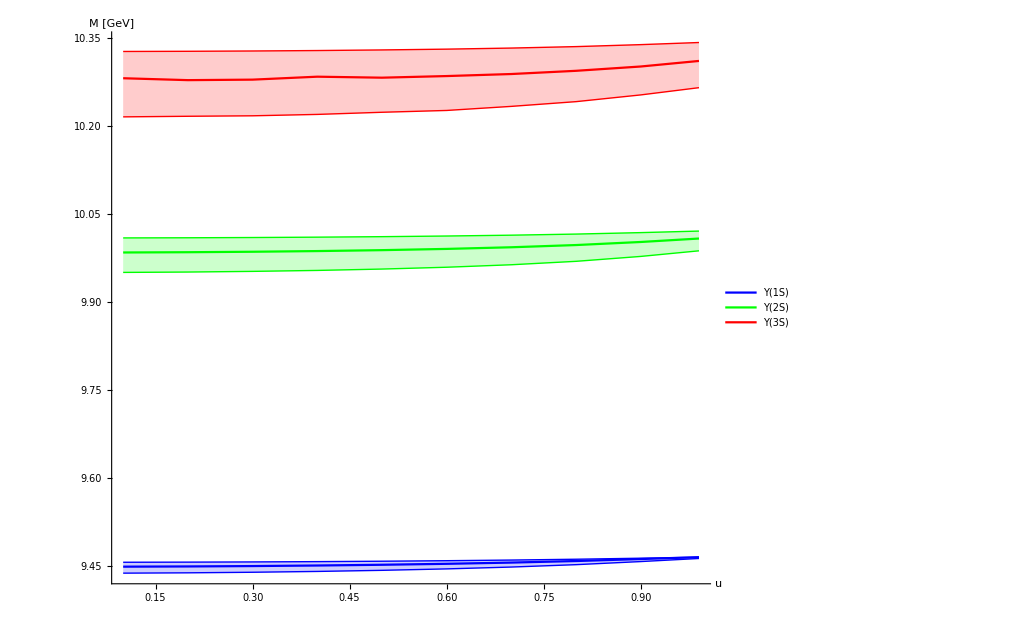

```mathematica
ListPlot[{Transpose[{uscan[[;;]],wrfitbb1[[;;,2]]}],Transpose[{uscan[[;;]],wrfitbb1[[;;,3]]}],Transpose[{uscan[[;;]],wrfitbb1[[;;,4]]}],Transpose[{uscan[[;;]],wrfitbb2[[;;,2]]}],Transpose[{uscan[[;;]],wrfitbb2[[;;,3]]}],Transpose[{uscan[[;;]],wrfitbb2[[;;,4]]}],Transpose[{uscan[[;;]],wrfitbb3[[;;,2]]}],Transpose[{uscan[[;;]],wrfitbb3[[;;,3]]}],Transpose[{uscan[[;;]],wrfitbb3[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["Υ(1S)",25,"Helvetica"],None,None,Style["Υ(2S)",25,"Helvetica"],None,None,Style["Υ(3S)",25,"Helvetica"]}],{0.8,0.4}]]
```

```mathematica
Transpose[{uscan,gfitbb[[All,1]],gfitbbu[[All,1]],gfitbbl[[All,1]]}]
```

{{1/10,0.00738667,0.0126786,0.00307764},{1/5,0.00737527,0.0126736,0.00306854},{3/10,0.00735164,0.012659,0.00305036},{2/5,0.00730928,0.0126239,0.00302305},{1/2,0.00723688,0.0125489,0.00297937},{3/5,0.00711366,0.0123987,0.00291069},{7/10,0.00689785,0.0121046,0.00279992},{4/5,0.00650054,0.0115117,0.00261017},{9/10,0.00565336,0.0101518,0.00223109},{99/100,0.0028416,0.00528984,0.00107254}}

```mathematica
gfitbb1={{1/10,0.00738667140489188,0.012678580135118784,0.0030776439465828504},{1/5,0.007375271851376379,0.012673564304510951,0.0030685427032178525},{3/10,0.007351637130377281,0.012658958526613466,0.003050361568656736},{2/5,0.007309279747997597,0.012623918574300627,0.0030230469689283305},{1/2,0.0072368805496368675,0.012548890123624193,0.0029793690338808486},{3/5,0.007113662758503195,0.012398683530073892,0.0029106851751723698},{7/10,0.006897852716221106,0.012104624337847272,0.0027999206510812454},{4/5,0.006500544778925407,0.011511705562737307,0.002610167540653337},{9/10,0.005653364362888479,0.010151779069869055,0.0022310889082230168},{99/100,0.0028415967857800865,0.005289842045874265,0.001072544839667232}};
```

```mathematica
gfitbb1inter=Interpolation[gfitbb1[[All,;;2]],InterpolationOrder->1];
gfitbb1interl=Interpolation[gfitbb1[[All,1;;3;;2]],InterpolationOrder->1];
gfitbb1interu=Interpolation[gfitbb1[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitbb1inter[0],gfitbb1interl[0],gfitbb1interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.00739807,0.0126836,0.00308675}

```mathematica
gfitbb1n=Join[{{0,0.00739807095840738,0.012683595965726617,0.0030867451899478484}},gfitbb1]
```

{{0,0.00739807,0.0126836,0.00308675},{1/10,0.00738667,0.0126786,0.00307764},{1/5,0.00737527,0.0126736,0.00306854},{3/10,0.00735164,0.012659,0.00305036},{2/5,0.00730928,0.0126239,0.00302305},{1/2,0.00723688,0.0125489,0.00297937},{3/5,0.00711366,0.0123987,0.00291069},{7/10,0.00689785,0.0121046,0.00279992},{4/5,0.00650054,0.0115117,0.00261017},{9/10,0.00565336,0.0101518,0.00223109},{99/100,0.0028416,0.00528984,0.00107254}}

```mathematica
gfitbb1inter=Interpolation[gfitbb1n[[All,;;2]],InterpolationOrder->5];
gfitbb1interl=Interpolation[gfitbb1n[[All,1;;3;;2]],InterpolationOrder->5];
gfitbb1interu=Interpolation[gfitbb1n[[All,1;;4;;3]],InterpolationOrder->5];
```

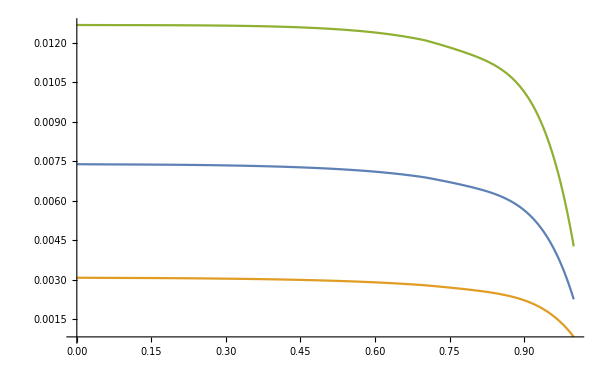

```mathematica
Plot[{gfitbb1inter[x],gfitbb1interu[x],gfitbb1interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/Upsilon1_width_T150_par.dat",Table[{u,gfitbb1inter[u],gfitbb1interu[u],gfitbb1interl[u]},{u,0,1,1/20}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Upsilon1_width_T150_par.dat

```mathematica
Transpose[{uscan,gfitbb[[All,2]],gfitbbu[[All,2]],gfitbbl[[All,2]]}]
```

{{1/10,0.0476739,0.0765324,0.0213499},{1/5,0.0477663,0.0768592,0.0213365},{3/10,0.0478998,0.0772747,0.021304},{2/5,0.0480391,0.0780277,0.0212334},{1/2,0.0481172,0.078649,0.021092},{3/5,0.0480121,0.0792582,0.0208189},{7/10,0.0474745,0.0793946,0.020298},{4/5,0.0459332,0.0782502,0.0192694},{9/10,0.0415782,0.0728634,0.0169452},{99/100,0.0231272,0.0436857,0.00875864}}

```mathematica
gfitbb2={{1/10,0.047673949000464025,0.07653239332699067,0.02134986945608235},{1/5,0.04776628697789676,0.07685920634000984,0.021336500348199703},{3/10,0.04789979277547312,0.07727466909105475,0.02130403556717},{2/5,0.04803912612471308,0.07802766552317551,0.021233402349420675},{1/2,0.0481172251269611,0.07864899156451685,0.02109195343647033},{3/5,0.04801212227028091,0.07925817285983457,0.020818859759866033},{7/10,0.04747449361865648,0.07939457421838048,0.02029800831328093},{4/5,0.045933221418702194,0.07825021997809167,0.01926936317293007},{9/10,0.04157822515135499,0.07286341592538396,0.016945174773009494},{99/100,0.023127229354214875,0.043685741898337814,0.008758639548419496}};
```

```mathematica
gfitbb2inter=Interpolation[gfitbb2[[All,;;2]],InterpolationOrder->1];
gfitbb2interl=Interpolation[gfitbb2[[All,1;;3;;2]],InterpolationOrder->1];
gfitbb2interu=Interpolation[gfitbb2[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitbb2inter[0],gfitbb2interl[0],gfitbb2interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.0475816,0.0762056,0.0213632}

```mathematica
gfitbb2n=Join[{{0,0.04758161102303129,0.07620558031397151,0.021363238563964996}},gfitbb2]
```

{{0,0.0475816,0.0762056,0.0213632},{1/10,0.0476739,0.0765324,0.0213499},{1/5,0.0477663,0.0768592,0.0213365},{3/10,0.0478998,0.0772747,0.021304},{2/5,0.0480391,0.0780277,0.0212334},{1/2,0.0481172,0.078649,0.021092},{3/5,0.0480121,0.0792582,0.0208189},{7/10,0.0474745,0.0793946,0.020298},{4/5,0.0459332,0.0782502,0.0192694},{9/10,0.0415782,0.0728634,0.0169452},{99/100,0.0231272,0.0436857,0.00875864}}

```mathematica
gfitbb2inter=Interpolation[gfitbb2n[[All,;;2]],InterpolationOrder->5];
gfitbb2interl=Interpolation[gfitbb2n[[All,1;;3;;2]],InterpolationOrder->5];
gfitbb2interu=Interpolation[gfitbb2n[[All,1;;4;;3]],InterpolationOrder->5];
```

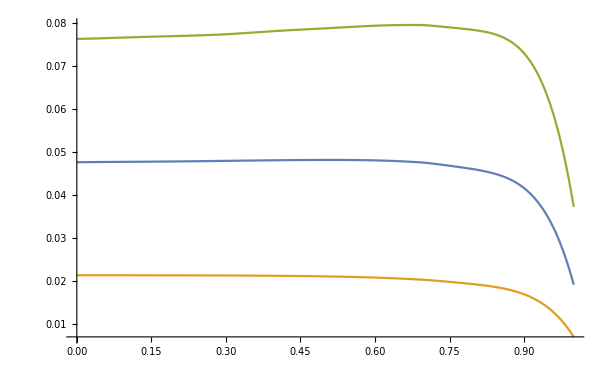

```mathematica
Plot[{gfitbb2inter[x],gfitbb2interu[x],gfitbb2interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/Upsilon2_width_T150_par.dat",Table[{u,gfitbb2inter[u],gfitbb2interu[u],gfitbb2interl[u]},{u,0,1,1/20}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Upsilon2_width_T150_par.dat

```mathematica
Transpose[{uscan,gfitbb[[All,3]],gfitbbu[[All,3]],gfitbbl[[All,3]]}]
```

{{1/10,0.110706,0.15777,0.0611815},{1/5,0.116872,0.157878,0.0612599},{3/10,0.117735,0.160153,0.0612993},{2/5,0.113138,0.161887,0.0613717},{1/2,0.119625,0.16483,0.0613303},{3/5,0.120641,0.167713,0.061088},{7/10,0.121259,0.17077,0.0601987},{4/5,0.119899,0.172407,0.0580282},{9/10,0.113658,0.169739,0.0523242},{99/100,0.0738625,0.122721,0.0287306}}

```mathematica
gfitbb3={{1/10,0.11070585204584911,0.15776976844952623,0.061181452108719024},{1/5,0.1168717447870786,0.1578781324702774,0.06125985494307562},{3/10,0.11773501277968197,0.1601532233439504,0.061299295806732185},{2/5,0.11313823000397731,0.1618869970396518,0.06137173170794632},{1/2,0.11962455894279599,0.16482962967263817,0.06133025456088586},{3/5,0.12064052980055034,0.16771306878697348,0.06108803137590968},{7/10,0.12125878183306399,0.17076992243950473,0.060198715125607656},{4/5,0.11989921142504663,0.17240705999446687,0.058028176290812465},{9/10,0.11365804754149299,0.16973902547909717,0.052324223424020495},{99/100,0.07386252392637095,0.12272086945829737,0.02873058618103025}};
```

```mathematica
gfitbb3inter=Interpolation[Delete[gfitbb3[[All,;;2]],{{1},{4}}],InterpolationOrder->1];
gfitbb3interl=Interpolation[gfitbb3[[All,1;;3;;2]],InterpolationOrder->1];
gfitbb3interu=Interpolation[gfitbb3[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitbb3inter[0],gfitbb3interl[0],gfitbb3interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.115145,0.157661,0.061103}

```mathematica
gfitbb3n=Join[{{0,0.11514520880187185,0.15766140442877505,0.06110304927436243}},Delete[gfitbb3,{{1},{4}}]]
```

{{0,0.115145,0.157661,0.061103},{1/5,0.116872,0.157878,0.0612599},{3/10,0.117735,0.160153,0.0612993},{1/2,0.119625,0.16483,0.0613303},{3/5,0.120641,0.167713,0.061088},{7/10,0.121259,0.17077,0.0601987},{4/5,0.119899,0.172407,0.0580282},{9/10,0.113658,0.169739,0.0523242},{99/100,0.0738625,0.122721,0.0287306}}

```mathematica
gfitbb3inter=Interpolation[gfitbb3n[[All,;;2]],InterpolationOrder->5];
gfitbb3interl=Interpolation[gfitbb3n[[All,1;;3;;2]],InterpolationOrder->5];
gfitbb3interu=Interpolation[gfitbb3n[[All,1;;4;;3]],InterpolationOrder->5];
```

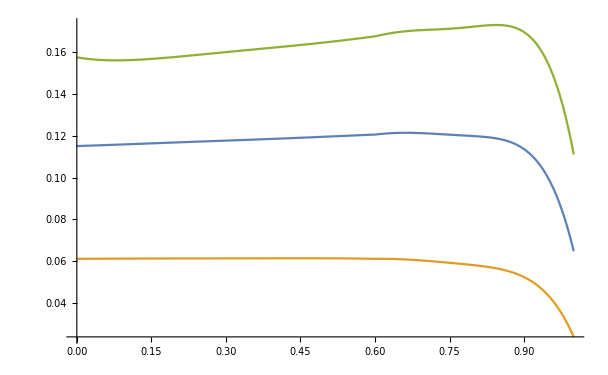

```mathematica
Plot[{gfitbb3inter[x],gfitbb3interu[x],gfitbb3interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/Upsilon3_width_T150_par.dat",Table[{u,gfitbb3inter[u],gfitbb3interu[u],gfitbb3interl[u]},{u,0,1,1/20}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Upsilon3_width_T150_par.dat

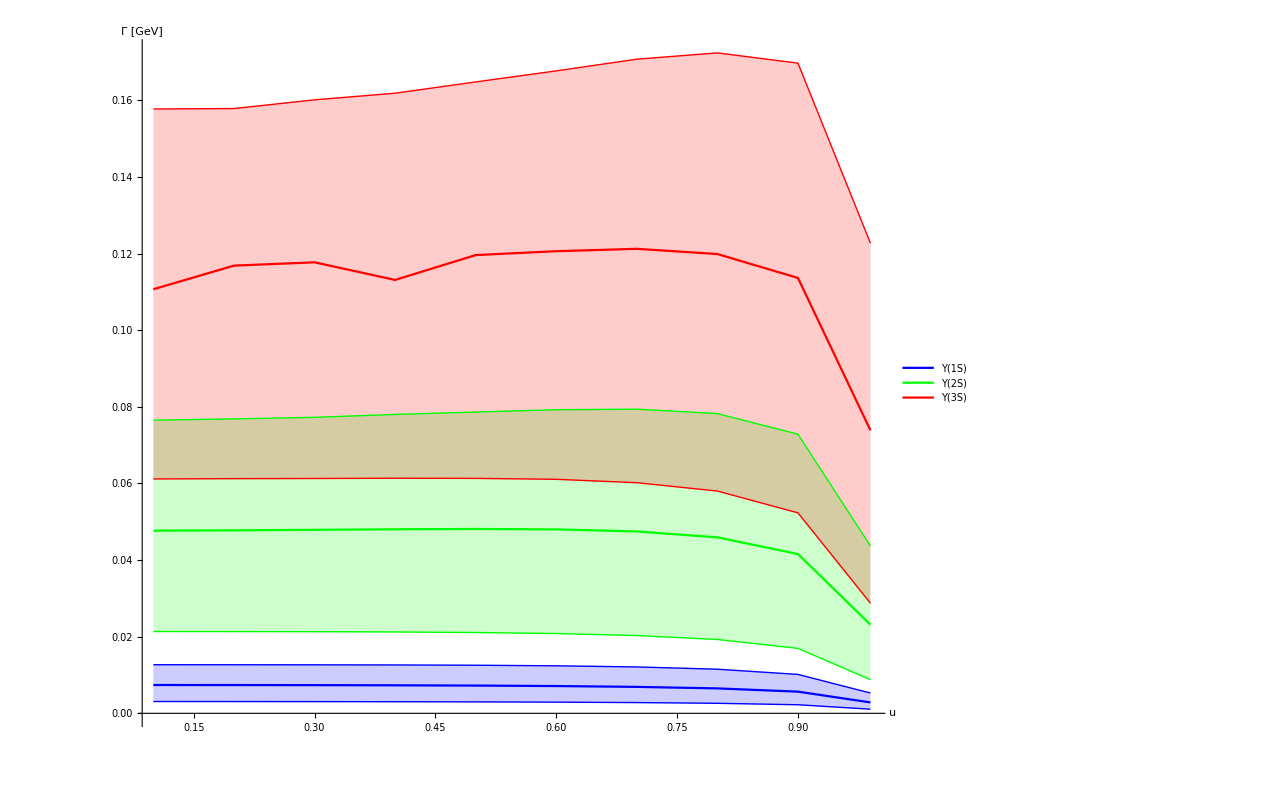

```mathematica
ListPlot[{Transpose[{uscan[[;;]],gfitbb1[[;;,2]]}],Transpose[{uscan[[;;]],gfitbb1[[;;,3]]}],Transpose[{uscan[[;;]],gfitbb1[[;;,4]]}],Transpose[{uscan[[;;]],gfitbb2[[;;,2]]}],Transpose[{uscan[[;;]],gfitbb2[[;;,3]]}],Transpose[{uscan[[;;]],gfitbb2[[;;,4]]}],Transpose[{uscan[[;;]],gfitbb3[[;;,2]]}],Transpose[{uscan[[;;]],gfitbb3[[;;,3]]}],Transpose[{uscan[[;;]],gfitbb3[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["Υ(1S)",25,"Helvetica"],None,None,Style["Υ(2S)",25,"Helvetica"],None,None,Style["Υ(3S)",25,"Helvetica"]}],{0.8,0.4}]]
```

#### Charmonium 250 MeV Parallel

```mathematica
Do[ccdata[n]=Import["cc/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[ccdatau[n]=Import["cc/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250u.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[ccdatal[n]=Import["cc/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250l.dat"];,{n,Length[uscan]}];
```

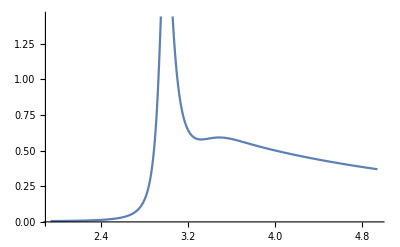

```mathematica
Block[{n=9},ListPlot[{ccdata[n]},Joined->True]]
```

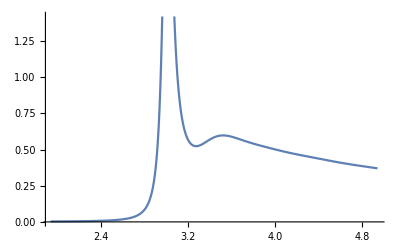

```mathematica
Block[{n=10},ListPlot[{ccdata[n]},Joined->True]]
```

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata,ccmodel,uscanI]];
Quiet[fit[ccdatal,ccmodell,uscanI]];
Quiet[fit[ccdatau,ccmodelu,uscanI]];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[wr,wrfitccl,ccmodell];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitcc,ccmodel];
store[Γ,gfitccl,ccmodell];
store[Γ,gfitccu,ccmodelu];
store[const,cfitcc,ccmodel];
store[const,cfitccl,ccmodell];
store[const,cfitccu,ccmodelu];
store[δbg,dfitcc,ccmodel];
store[δbg,dfitccl,ccmodell];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitcc,ccmodel];
store[shift,sfitccl,ccmodell];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitcc,ccmodel];
store[shift2,s2fitccl,ccmodell];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitcc,ccmodel];
storearea[areafitccl,ccmodell];
storearea[areafitccu,ccmodelu];
```

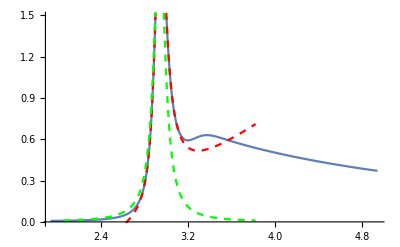

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

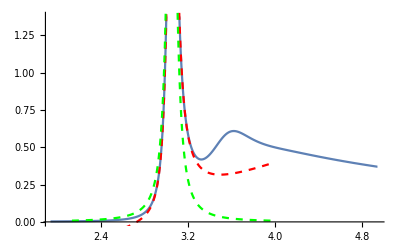

```mathematica
Block[{i=10,ii=1},Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

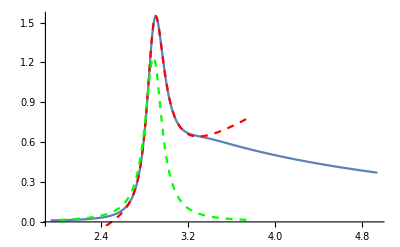

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
Transpose[{uscan,wrfitcc[[All,1]],wrfitccu[[All,1]],wrfitccl[[All,1]]}]
```

{{1/10,2.93849,2.88256,3.00182},{1/5,2.93946,2.88378,3.00276},{3/10,2.94114,2.88594,3.00437},{2/5,2.94369,2.88923,3.00675},{1/2,2.94737,2.89413,3.01006},{3/5,2.95256,2.90113,3.01454},{7/10,2.95999,2.91136,3.02057},{4/5,2.97084,2.92642,3.02877},{9/10,2.98724,2.94901,3.04003},{99/100,3.00542,2.97063,3.04957}}

```mathematica
wrfit250cc1={{1/10,2.938494799060516,2.882562362295467,3.001821344113262},{1/5,2.9394559423960387,2.883784173840891,3.0027557058815386},{3/10,2.941142865567031,2.885944450179504,3.0043699739118774},{2/5,2.9436884992112677,2.8892327485851133,3.0067541114739997},{1/2,2.9473705457879396,2.894130928244887,3.0100586789736403},{3/5,2.952563667973968,2.9011256303290076,3.014538203042748},{7/10,2.9599884103719787,2.9113606122302897,3.0205708798136883},{4/5,2.970842271452593,2.9264223951462536,3.0287706090448294},{9/10,2.987243316192745,2.949014757062738,3.04002967953725},{99/100,3.0054192293304074,2.970627428039877,3.049568348994802}};
```

```mathematica
wrfit250cc1[[All,2]]/wrfit250cc1[[All,3]]
```

{1.0194,1.01931,1.01913,1.01885,1.0184,1.01773,1.0167,1.01518,1.01296,1.01171}

```mathematica
wrfit250cc1[[All,2]]/wrfit250cc1[[All,4]]
```

{0.978904,0.978919,0.978955,0.979025,0.979174,0.979441,0.979943,0.980874,0.982636,0.985523}

```mathematica
wrfitcc1inter=Interpolation[wrfit250cc1[[All,;;2]],InterpolationOrder->1];
wrfitcc1interl=Interpolation[wrfit250cc1[[All,1;;3;;2]],InterpolationOrder->1];
wrfitcc1interu=Interpolation[wrfit250cc1[[All,1;;4;;3]],InterpolationOrder->1];
Export["final/Jpsi_mass_T250_par.dat",Join[{{0,wrfitcc1inter[0],wrfitcc1interl[0],wrfitcc1interu[0]}},wrfit250cc1]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Jpsi_mass_T250_par.dat

```mathematica
Transpose[{uscan,gfitcc[[All,1]],gfitccu[[All,1]],gfitccl[[All,1]]}]
```

{{1/10,0.121779,0.190864,0.135141},{1/5,0.122927,0.19307,0.135871},{3/10,0.12484,0.196813,0.137077},{2/5,0.127624,0.202139,0.138683},{1/2,0.131087,0.209035,0.140598},{3/5,0.135274,0.217263,0.14254},{7/10,0.139633,0.226165,0.14393},{4/5,0.142868,0.23352,0.143362},{9/10,0.140075,0.232118,0.136105},{99/100,0.0977839,0.175447,0.0886082}}

```mathematica
gfit250cc10={{1/10,0.12177866636404133,0.190864327970717,0.13514149712979748},{1/5,0.12292700166903985,0.1930695199416454,0.13587061091630212},{3/10,0.12483969498098495,0.19681343903831175,0.13707651710318555},{2/5,0.12762422635379797,0.20213935154522475,0.13868261599270054},{1/2,0.1310867413071019,0.20903474864685098,0.1405978762945484},{3/5,0.13527400971282658,0.2172626595081938,0.142539813078063},{7/10,0.13963269497401512,0.22616471862288864,0.14393035713543043},{4/5,0.14286846270865178,0.23352002012363038,0.1433620816139026},{9/10,0.14007501902262293,0.23211845928137384,0.13610496039075892},{99/100,0.09778387908726002,0.17544682840606363,0.08860817730316421}};
```

```mathematica
gfit250cc1=gfit250cc10/.{a_,b_,c_,d_}:>{a,b+1/2(c-d),c,b}
```

{{1/10,0.14964,0.190864,0.121779},{1/5,0.151526,0.19307,0.122927},{3/10,0.154708,0.196813,0.12484},{2/5,0.159353,0.202139,0.127624},{1/2,0.165305,0.209035,0.131087},{3/5,0.172635,0.217263,0.135274},{7/10,0.18075,0.226165,0.139633},{4/5,0.187947,0.23352,0.142868},{9/10,0.188082,0.232118,0.140075},{99/100,0.141203,0.175447,0.0977839}}

```mathematica
gfitcc1inter=Interpolation[gfit250cc1[[All,;;2]],InterpolationOrder->1];
gfitcc1interl=Interpolation[gfit250cc1[[All,1;;3;;2]],InterpolationOrder->1];
gfitcc1interu=Interpolation[gfit250cc1[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitcc1inter[0],gfitcc1interl[0],gfitcc1interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.147754,0.188659,0.12063}

```mathematica
gfitcc1n=Join[{{0,0.14775370738729074,0.18865913599978862,0.12063033105904282}},gfit250cc1]
```

{{0,0.147754,0.188659,0.12063},{1/10,0.14964,0.190864,0.121779},{1/5,0.151526,0.19307,0.122927},{3/10,0.154708,0.196813,0.12484},{2/5,0.159353,0.202139,0.127624},{1/2,0.165305,0.209035,0.131087},{3/5,0.172635,0.217263,0.135274},{7/10,0.18075,0.226165,0.139633},{4/5,0.187947,0.23352,0.142868},{9/10,0.188082,0.232118,0.140075},{99/100,0.141203,0.175447,0.0977839}}

```mathematica
gfitcc1inter=Interpolation[gfitcc1n[[All,;;2]],InterpolationOrder->5];
gfitcc1interl=Interpolation[gfitcc1n[[All,1;;3;;2]],InterpolationOrder->5];
gfitcc1interu=Interpolation[gfitcc1n[[All,1;;4;;3]],InterpolationOrder->5];
```

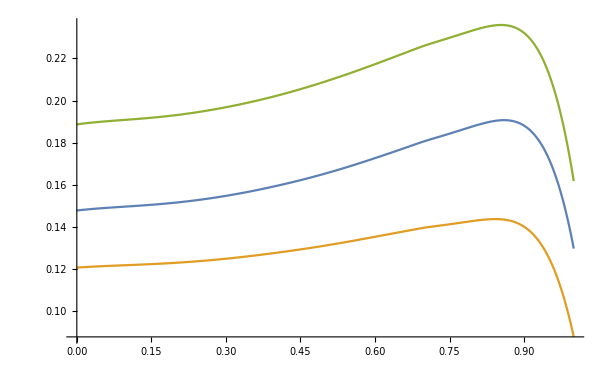

```mathematica
Plot[{gfitcc1inter[x],gfitcc1interu[x],gfitcc1interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/psip_width_T250_par.dat",Table[{u,gfitcc1inter[u],gfitcc1interu[u],gfitcc1interl[u]},{u,0,1,1/20}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/psip_width_T250_par.dat

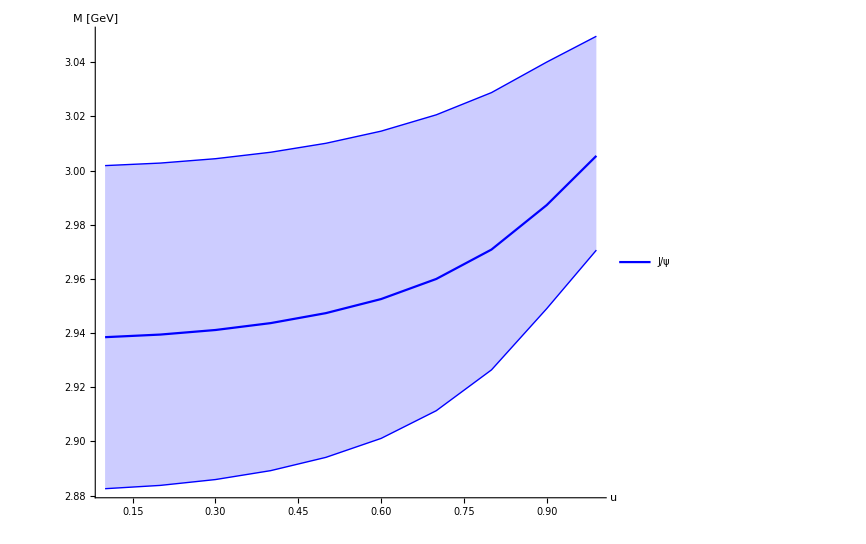

```mathematica
ListPlot[{Transpose[{uscan[[;;]],wrfit250cc1[[;;,2]]}],Transpose[{uscan[[;;]],wrfit250cc1[[;;,3]]}],Transpose[{uscan[[;;]],wrfit250cc1[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"]}],{0.8,0.2}]]
```

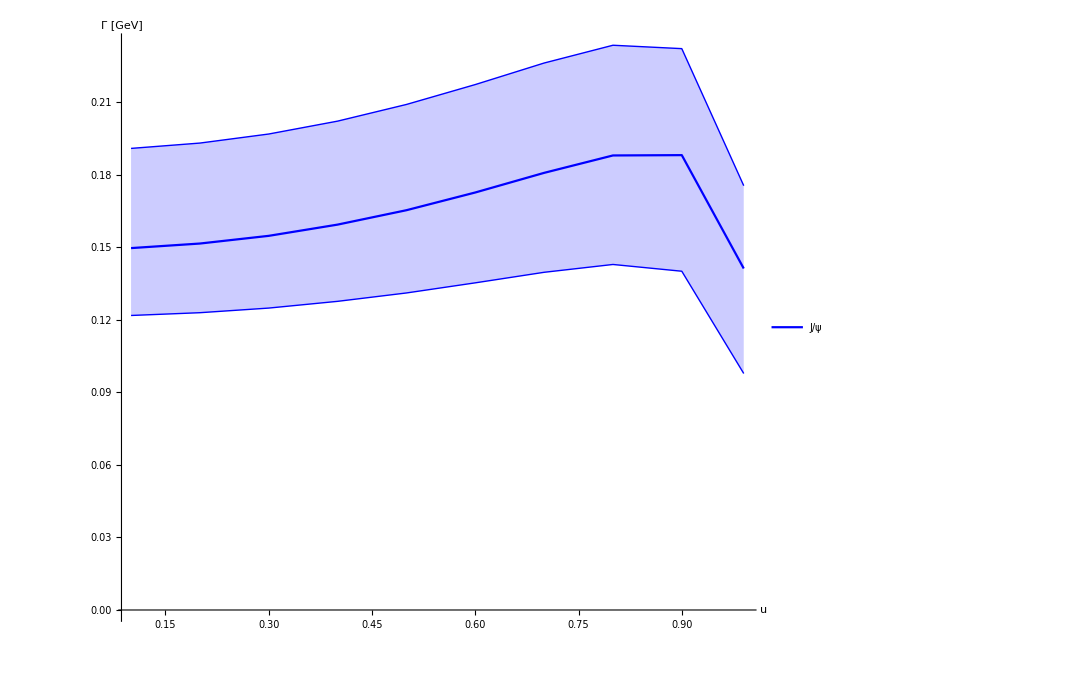

```mathematica
ListPlot[{Transpose[{uscan[[;;]],gfit250cc1[[;;,2]]}],Transpose[{uscan[[;;]],gfit250cc1[[;;,3]]}],Transpose[{uscan[[;;]],gfit250cc1[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"]}],{0.8,0.2}]]
```

#### Bottomonium 250 MeV Parallel

```mathematica
Do[bbdata[n]=Import["bb/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[bbdatau[n]=Import["bb/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250u.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[bbdatal[n]=Import["bb/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250l.dat"];,{n,Length[uscan]}];
```

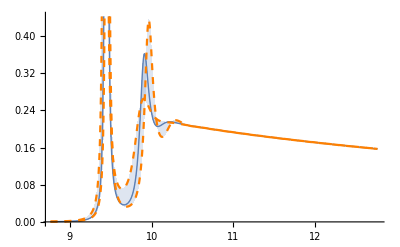

```mathematica
Block[{n=10},ListPlot[{bbdata[n],bbdatal[n],bbdatau[n]},Joined->True,Filling->{1->{2},1->{3}},PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[bbmodelu,bbmodell,bbmodel]
Quiet[fit[bbdata,bbmodel,uscanI]];
Quiet[fit[bbdatal,bbmodell,uscanI]];
Quiet[fit[bbdatau,bbmodelu,uscanI]];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[wr,wrfitbbl,bbmodell];
store[wr,wrfitbbu,bbmodelu];
store[Γ,gfitbb,bbmodel];
store[Γ,gfitbbl,bbmodell];
store[Γ,gfitbbu,bbmodelu];
store[const,cfitbb,bbmodel];
store[const,cfitbbl,bbmodell];
store[const,cfitbbu,bbmodelu];
store[δbg,dfitbb,bbmodel];
store[δbg,dfitbbl,bbmodell];
store[δbg,dfitbbu,bbmodelu];
store[shift,sfitbb,bbmodel];
store[shift,sfitbbl,bbmodell];
store[shift,sfitbbu,bbmodelu];
store[shift2,s2fitbb,bbmodel];
store[shift2,s2fitbbl,bbmodell];
store[shift2,s2fitbbu,bbmodelu];
storearea[areafitbb,bbmodel];
storearea[areafitbbl,bbmodell];
storearea[areafitbbu,bbmodelu];
```

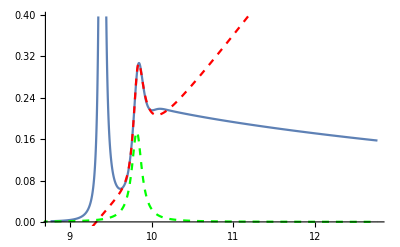

```mathematica
Block[{i=1,ii=2},Show[{ListPlot[bbdata[i],Joined->True],Plot[BW[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],dfitbb[[i,ii]],cfitbb[[i,ii]],sfitbb[[i,ii]],s2fitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],cfitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

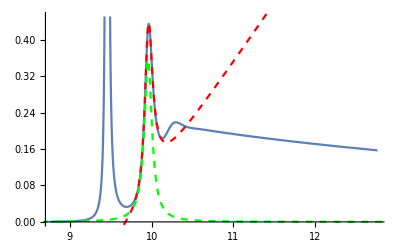

```mathematica
Block[{i=10,ii=2},Show[{ListPlot[bbdatal[i],Joined->True],Plot[BW[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],dfitbbl[[i,ii]],cfitbbl[[i,ii]],sfitbbl[[i,ii]],s2fitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],cfitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

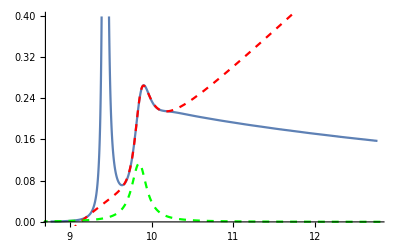

```mathematica
Block[{i=10,ii=2},Show[{ListPlot[bbdatau[i],Joined->True],Plot[BW[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],dfitbbu[[i,ii]],cfitbbu[[i,ii]],sfitbbu[[i,ii]],s2fitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],cfitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
Transpose[{uscan,wrfitbb[[All,1]],wrfitbbu[[All,1]],wrfitbbl[[All,1]]}]
```

{{1/10,9.3931,9.36255,9.41924},{1/5,9.39416,9.36384,9.42004},{3/10,9.39595,9.36606,9.42141},{2/5,9.39858,9.36932,9.4234},{1/2,9.40215,9.37378,9.4261},{3/5,9.40688,9.37972,9.42963},{7/10,9.41309,9.3876,9.43421},{4/5,9.42132,9.39818,9.44018},{9/10,9.43252,9.41285,9.44809},{99/100,9.44495,9.42954,9.4563}}

```mathematica
wrfit250bb1={{1/10,9.393104687961864,9.362547491966819,9.41923794150853},{1/5,9.394155553275727,9.363842209192038,9.420041097667497},{3/10,9.395953853924139,9.366062749893455,9.421411409700704},{2/5,9.398577575081315,9.369315474982715,9.423401513367551},{1/2,9.402153271924162,9.373775262095739,9.426096368107412},{3/5,9.406882680432703,9.379716783347645,9.4296289346582},{7/10,9.413090504644966,9.387595237920163,9.434209966583271},{4/5,9.421323536178017,9.398184093513313,9.440182188909652},{9/10,9.432524980520716,9.412852232106802,9.448094359877707},{99/100,9.444948709516142,9.429543896525654,9.456300269110352}};
```

```mathematica
wrfitbb31inter=Interpolation[wrfit250bb1[[All,;;2]],InterpolationOrder->1];
wrfitbb31interl=Interpolation[wrfit250bb1[[All,1;;3;;2]],InterpolationOrder->1];
wrfitbb31interu=Interpolation[wrfit250bb1[[All,1;;4;;3]],InterpolationOrder->1];
Export["final/Upsilon1_mass_T250_par.dat",N[Join[{{0,wrfitbb31inter[0],wrfitbb31interl[0],wrfitbb31interu[0]}},wrfitbb31]]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Upsilon1_mass_T250_par.dat

```mathematica
Transpose[{uscan,wrfitbb[[All,2]],wrfitbbu[[All,2]],wrfitbbl[[All,2]]}]
```

{{1/10,9.81888,9.74796,9.89749},{1/5,9.81978,9.74907,9.89852},{3/10,9.82118,9.75073,9.90005},{2/5,9.82372,9.7537,9.90255},{1/2,9.82719,9.75789,9.90595},{3/5,9.8323,9.76505,9.91068},{7/10,9.84059,9.77559,9.91731},{4/5,9.85252,9.79201,9.92631},{9/10,9.87081,9.8187,9.93985},{99/100,9.89787,9.84675,9.95711}}

```mathematica
wrfit250bb2={{1/10,9.8188847448219,9.747958725365306,9.897489887998114},{1/5,9.819784303968316,9.749071881251743,9.898522304345137},{3/10,9.82117828563342,9.750730283715242,9.90004841603917},{2/5,9.823721583473032,9.75370092184241,9.902549152424882},{1/2,9.827186025747848,9.757886235074904,9.905947980420223},{3/5,9.832300507609991,9.765053706024757,9.910678834537448},{7/10,9.840594165112748,9.775587450226777,9.917311561167626},{4/5,9.852518134557833,9.792008165639125,9.926311119834589},{9/10,9.870811400096663,9.818701549492065,9.939852565883442},{99/100,9.897873001778587,9.846748613652471,9.957105424419845}};
```

```mathematica
wrfitbb2inter=Interpolation[wrfit250bb2[[All,;;2]],InterpolationOrder->1];
wrfitbb2interl=Interpolation[wrfit250bb2[[All,1;;3;;2]],InterpolationOrder->1];
wrfitbb2interu=Interpolation[wrfit250bb2[[All,1;;4;;3]],InterpolationOrder->1];
Export["final/data/Upsilon2_mass_T250_par.dat",N[Join[{{0,wrfitbb2inter[0],wrfitbb2interl[0],wrfitbb2interu[0]}},wrfit250bb2]]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/data/Upsilon2_mass_T250_par.dat

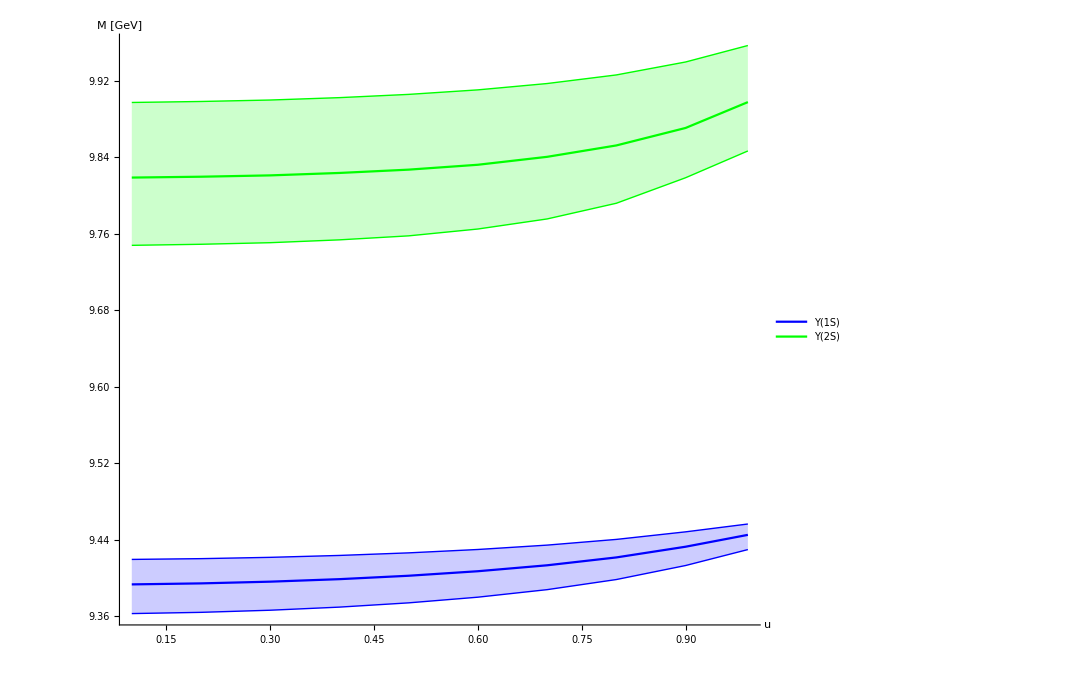

```mathematica
ListPlot[{Transpose[{uscan[[;;]],wrfit250bb1[[;;,2]]}],Transpose[{uscan[[;;]],wrfit250bb1[[;;,3]]}],Transpose[{uscan[[;;]],wrfit250bb1[[;;,4]]}],Transpose[{uscan[[;;]],wrfit250bb2[[;;,2]]}],Transpose[{uscan[[;;]],wrfit250bb2[[;;,3]]}],Transpose[{uscan[[;;]],wrfit250bb2[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["Υ(1S)",25,"Helvetica"],None,None,Style["Υ(2S)",25,"Helvetica"],None,None}],{0.8,0.4}]]
```

```mathematica
Transpose[{uscan,gfitbb[[All,1]],gfitbbu[[All,1]],gfitbbl[[All,1]]}]
```

{{1/10,0.02975,0.045509,0.032729},{1/5,0.0298233,0.0457028,0.03276},{3/10,0.0299341,0.0460166,0.0327974},{2/5,0.0300613,0.04642,0.0328151},{1/2,0.0301665,0.0468608,0.0327659},{3/5,0.0301742,0.047245,0.0325625},{7/10,0.029931,0.0473437,0.0320314},{4/5,0.029074,0.0466062,0.0307749},{9/10,0.0264545,0.0432445,0.0275664},{99/100,0.0148966,0.0256015,0.0149585}}

```mathematica
gfit250bb1={{1/10,0.0297499852972095,0.04550897431680757,0.032728968500481743},{1/5,0.029823268671945968,0.04570280015015007,0.03275999669757328},{3/10,0.029934112567759224,0.04601663843549272,0.032797407521443035},{2/5,0.03006131075116736,0.046419989445103546,0.03281512085093753},{1/2,0.03016646153064735,0.046860794133702414,0.03276590443252528},{3/5,0.03017423076480074,0.04724504552854119,0.03256247094782374},{7/10,0.029931016157782677,0.04734366070489565,0.03203135656629024},{4/5,0.029074023307888396,0.04660617880527519,0.03077488761073282},{9/10,0.02645450659024534,0.04324448775490233,0.027566355965207477},{99/100,0.01489657472056857,0.025601475662791796,0.014958458008823528}};
```

```mathematica
gfit250bb1=gfit250bb1/.{a_,b_,c_,d_}:>{a,b+1/2(c-d),c,b}
```

{{1/10,0.03614,0.045509,0.02975},{1/5,0.0362947,0.0457028,0.0298233},{3/10,0.0365437,0.0460166,0.0299341},{2/5,0.0368637,0.04642,0.0300613},{1/2,0.0372139,0.0468608,0.0301665},{3/5,0.0375155,0.047245,0.0301742},{7/10,0.0375872,0.0473437,0.029931},{4/5,0.0369897,0.0466062,0.029074},{9/10,0.0342936,0.0432445,0.0264545},{99/100,0.0202181,0.0256015,0.0148966}}

```mathematica
gfitbb1inter=Interpolation[gfit250bb1[[All,;;2]],InterpolationOrder->1];
gfitbb1interl=Interpolation[gfit250bb1[[All,1;;3;;2]],InterpolationOrder->1];
gfitbb1interu=Interpolation[gfit250bb1[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitbb1inter[0],gfitbb1interl[0],gfitbb1interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.0359853,0.0453151,0.0296767}

```mathematica
gfitbb1n=Join[{{0,0.03598530601251046,0.045315148483465066,0.029676701922473032}},gfit250bb1]
```

{{0,0.0359853,0.0453151,0.0296767},{1/10,0.03614,0.045509,0.02975},{1/5,0.0362947,0.0457028,0.0298233},{3/10,0.0365437,0.0460166,0.0299341},{2/5,0.0368637,0.04642,0.0300613},{1/2,0.0372139,0.0468608,0.0301665},{3/5,0.0375155,0.047245,0.0301742},{7/10,0.0375872,0.0473437,0.029931},{4/5,0.0369897,0.0466062,0.029074},{9/10,0.0342936,0.0432445,0.0264545},{99/100,0.0202181,0.0256015,0.0148966}}

```mathematica
gfitbb1inter=Interpolation[gfitbb1n[[All,;;2]],InterpolationOrder->5];
gfitbb1interl=Interpolation[gfitbb1n[[All,1;;3;;2]],InterpolationOrder->5];
gfitbb1interu=Interpolation[gfitbb1n[[All,1;;4;;3]],InterpolationOrder->5];
```

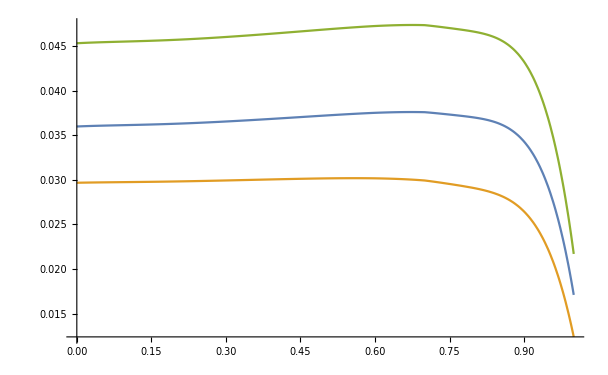

```mathematica
Plot[{gfitbb1inter[x],gfitbb1interu[x],gfitbb1interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/Upsilon1_width_T250_par.dat",Table[{u,gfitbb1inter[u],gfitbb1interu[u],gfitbb1interl[u]},{u,0,1,1/20}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Upsilon1_width_T250_par.dat

```mathematica
Transpose[{uscan,gfitbb[[All,2]],gfitbbu[[All,2]],gfitbbl[[All,2]]}]
```

{{1/10,0.147425,0.228761,0.165399},{1/5,0.148597,0.231698,0.16596},{3/10,0.151076,0.236281,0.167669},{2/5,0.154112,0.242879,0.169424},{1/2,0.158645,0.250892,0.172144},{3/5,0.164134,0.260935,0.174619},{7/10,0.169172,0.271395,0.176762},{4/5,0.174026,0.280722,0.176976},{9/10,0.172674,0.282501,0.169775},{99/100,0.12218,0.221617,0.113998}}

```mathematica
gfit250bb2={{1/10,0.14742502545091468,0.22876105583407824,0.16539922471817528},{1/5,0.14859737687314084,0.2316978275768727,0.1659603244286362},{3/10,0.15107629975509965,0.23628139510011067,0.16766866733490457},{2/5,0.15411155705354873,0.2428791906278738,0.1694243000388814},{1/2,0.1586450147739437,0.2508921765695187,0.17214417419391945},{3/5,0.1641335930086335,0.2609354064799014,0.1746192368141184},{7/10,0.1691724214326644,0.27139523906394336,0.17676169645392728},{4/5,0.1740260604107394,0.2807215820003511,0.17697579744173467},{9/10,0.1726739022286346,0.2825008501781205,0.16977545515684295},{99/100,0.12218008338753468,0.22161730132161495,0.11399808393162598}};
```

```mathematica
gfit250bb2=gfit250bb2/.{a_,b_,c_,d_}:>{a,b+1/2(c-d),c,b}
```

{{1/10,0.179106,0.228761,0.147425},{1/5,0.181466,0.231698,0.148597},{3/10,0.185383,0.236281,0.151076},{2/5,0.190839,0.242879,0.154112},{1/2,0.198019,0.250892,0.158645},{3/5,0.207292,0.260935,0.164134},{7/10,0.216489,0.271395,0.169172},{4/5,0.225899,0.280722,0.174026},{9/10,0.229037,0.282501,0.172674},{99/100,0.17599,0.221617,0.12218}}

```mathematica
gfitbb2inter=Interpolation[gfit250bb2[[All,;;2]],InterpolationOrder->1];
gfitbb2interl=Interpolation[gfit250bb2[[All,1;;3;;2]],InterpolationOrder->1];
gfitbb2interu=Interpolation[gfit250bb2[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitbb2inter[0],gfitbb2interl[0],gfitbb2interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.176746,0.225824,0.146253}

```mathematica
gfitbb2n=Join[{{0,0.17674575357047326,0.22582428409128377,0.14625267402868852}},gfit250bb2]
```

{{0,0.176746,0.225824,0.146253},{1/10,0.179106,0.228761,0.147425},{1/5,0.181466,0.231698,0.148597},{3/10,0.185383,0.236281,0.151076},{2/5,0.190839,0.242879,0.154112},{1/2,0.198019,0.250892,0.158645},{3/5,0.207292,0.260935,0.164134},{7/10,0.216489,0.271395,0.169172},{4/5,0.225899,0.280722,0.174026},{9/10,0.229037,0.282501,0.172674},{99/100,0.17599,0.221617,0.12218}}

```mathematica
gfitbb2inter=Interpolation[gfitbb2n[[All,;;2]],InterpolationOrder->5];
gfitbb2interl=Interpolation[gfitbb2n[[All,1;;3;;2]],InterpolationOrder->5];
gfitbb2interu=Interpolation[gfitbb2n[[All,1;;4;;3]],InterpolationOrder->5];
```

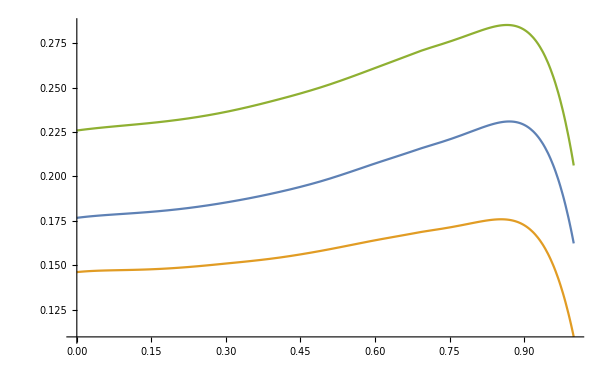

```mathematica
Plot[{gfitbb2inter[x],gfitbb2interu[x],gfitbb2interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/Upsilon2_width_T250_par.dat",Table[{u,gfitbb2inter[u],gfitbb2interu[u],gfitbb2interl[u]},{u,0,1,1/20}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Upsilon2_width_T250_par.dat

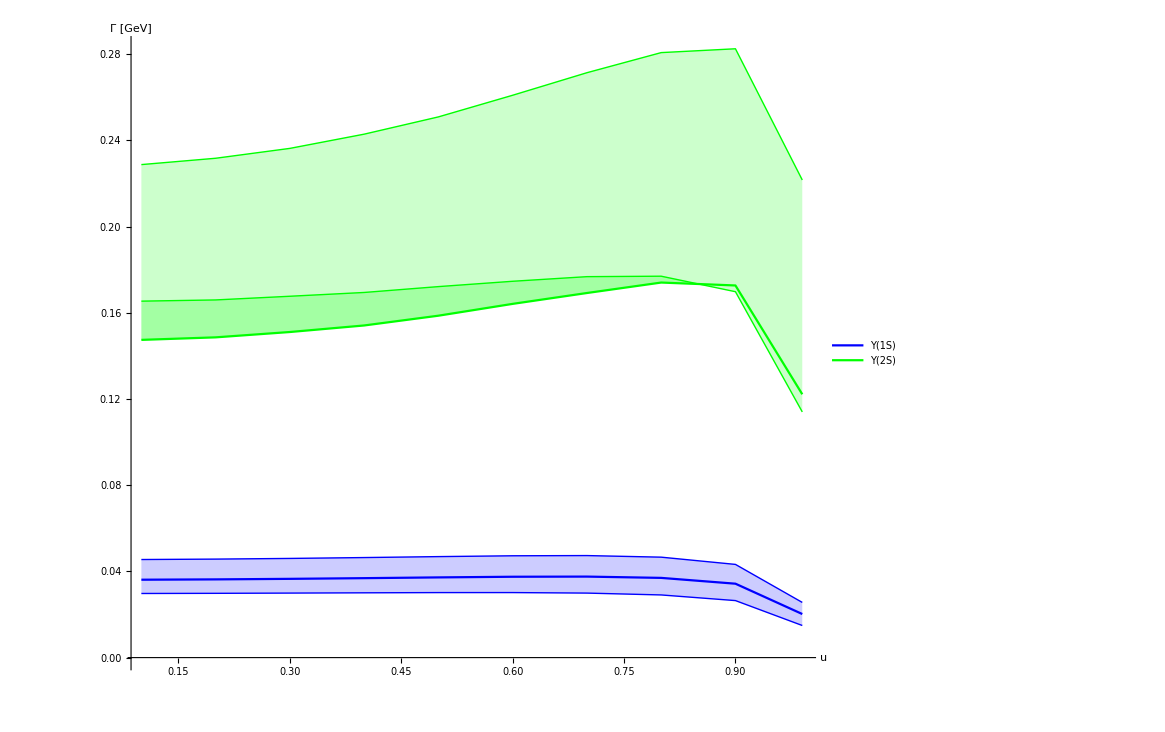

```mathematica
ListPlot[{Transpose[{uscan[[;;]],gfit250bb1[[;;,2]]}],Transpose[{uscan[[;;]],gfit250bb1[[;;,3]]}],Transpose[{uscan[[;;]],gfit250bb1[[;;,4]]}],Transpose[{uscan[[;;]],gfit250bb2[[;;,2]]}],Transpose[{uscan[[;;]],gfit250bb2[[;;,3]]}],Transpose[{uscan[[;;]],gfit250bb2[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["Υ(1S)",25,"Helvetica"],None,None,Style["Υ(2S)",25,"Helvetica"],None,None}],{0.8,0.4}]]
```

#### Charmonium Tc Perpendicular

```mathematica
Do[ccdata2[n]=Import["cc_perp/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectra.dat"];,{n,Length[uscanI]}];
```

```mathematica
Do[ccdata2u[n]=Import["cc_perp/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectrau.dat"];,{n,Length[uscanI1]}];
```

```mathematica
Do[ccdata2l[n]=Import["cc_perp/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectral.dat"];,{n,Length[uscanI1]}];
```

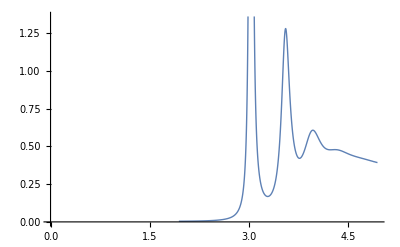

```mathematica
Block[{n=10},ListPlot[{ccdata2[n],ccdata2l[n],ccdata2u[n]},Joined->True,Filling->{1->{2},1->{3}},PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata2,ccmodel,uscanI]];
Quiet[fit[ccdata2l,ccmodell,uscanI1]];
Quiet[fit[ccdata2u,ccmodelu,uscanI1]];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[wr,wrfitccl,ccmodell];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitcc,ccmodel];
store[Γ,gfitccl,ccmodell];
store[Γ,gfitccu,ccmodelu];
store[const,cfitcc,ccmodel];
store[const,cfitccl,ccmodell];
store[const,cfitccu,ccmodelu];
store[δbg,dfitcc,ccmodel];
store[δbg,dfitccl,ccmodell];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitcc,ccmodel];
store[shift,sfitccl,ccmodell];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitcc,ccmodel];
store[shift2,s2fitccl,ccmodell];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitcc,ccmodel];
storearea[areafitccl,ccmodell];
storearea[areafitccu,ccmodelu];
```

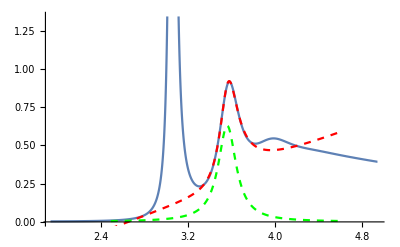

```mathematica
Block[{i=9,ii=2},Show[{ListPlot[ccdata2[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
Block[{i=10,ii=2},Show[{ListPlot[ccdata2l[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

-Graphics-

```mathematica
Block[{i=7,ii=2},Show[{ListPlot[ccdata2u[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

-Graphics-

```mathematica
Append[Transpose[{uscan1,wrfitcc[[;;9,1]],wrfitccu[[All,1]],wrfitccl[[All,1]]}],{uscan[[10]],wrfitcc[[10,1]]}]
```

{{1/10,3.06591,3.03852,3.08591},{1/5,3.06594,3.03846,3.08598},{3/10,3.06596,3.03833,3.08608},{2/5,3.06594,3.03807,3.08622},{1/2,3.06583,3.0376,3.08635},{3/5,3.06549,3.0367,3.08644},{7/10,3.06466,3.03499,3.08635},{4/5,3.06262,3.03144,3.08578},{9/10,3.05675,3.02252,3.0834},{99/100,3.02693}}

```mathematica
wrfitcc1={{1/10,3.0659136791211674,3.038519248859315,3.085908039438419},{1/5,3.0659362611599295,3.038457650089209,3.0859760129046734},{3/10,3.065955986092694,3.0383267091975794,3.086083427211389},{2/5,3.065944016889558,3.0380725790421246,3.0862163523876895},{1/2,3.065830272961793,3.0375978484844923,3.086351181910591},{3/5,3.065493331447631,3.036703685952488,3.086436867534},{7/10,3.064659924247268,3.0349867860854203,3.086354903891873},{4/5,3.062618842209552,3.031442953660978,3.0857779313075504},{9/10,3.0567545920013024,3.0225198055396247,3.0833998444900046},{99/100,3.026934352730806}};
```

```mathematica
wrfitcc1[[9,3]]/wrfitcc1[[9,2]]
```

0.9888

```mathematica
wrfitcc1[[9,4]]/wrfitcc1[[9,2]]
```

1.00872

```mathematica
wrfitcc1[[-1]]={wrfitcc1[[-1,1]],wrfitcc1[[-1,2]],wrfitcc1[[9,3]]/wrfitcc1[[9,2]] wrfitcc1[[-1,2]],wrfitcc1[[9,4]]/wrfitcc1[[9,2]] wrfitcc1[[-1,2]]};
```

```mathematica
wrfitcc1inter=Interpolation[wrfitcc1[[All,;;2]],InterpolationOrder->1];
wrfitcc1interl=Interpolation[wrfitcc1[[All,1;;3;;2]],InterpolationOrder->1];
wrfitcc1interu=Interpolation[wrfitcc1[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,wrfitcc1inter[0],wrfitcc1interl[0],wrfitcc1interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,3.06589,3.03858,3.08584}

```mathematica
Export["final/Jpsi_mass_T150_perp.dat",N[Join[{{0,wrfitcc1inter[0],wrfitcc1interl[0],wrfitcc1interu[0]}},wrfitcc1]]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Jpsi_mass_T150_perp.dat

```mathematica
Append[Transpose[{uscan1,wrfitcc[[;;9,2]],wrfitccu[[All,2]],wrfitccl[[All,2]]}],{uscan[[10]],wrfitcc[[10,2]]}]
```

{{1/10,3.58079,3.5042,3.64284},{1/5,3.58053,3.50377,3.64268},{3/10,3.58001,3.50342,3.64239},{2/5,3.5795,3.50262,3.64191},{1/2,3.57815,3.50191,3.64116},{3/5,3.57676,3.50053,3.63998},{7/10,3.57353,3.49869,3.63801},{4/5,3.56867,3.49662,3.63439},{9/10,3.55916,3.49316,3.62629},{99/100,3.54475}}

```mathematica
wrfitcc2={{1/10,3.580787697135326,3.504195680480768,3.642843665773438},{1/5,3.5805328268084256,3.503772674506767,3.642678292570941},{3/10,3.580008331703837,3.5034246384987675,3.642387795348624},{2/5,3.5795024822197883,3.502624657776248,3.6419123651827916},{1/2,3.5781490765490673,3.50191286673492,3.6411643536973206},{3/5,3.576755712372356,3.500534641878213,3.6399788653778606},{7/10,3.5735252142156972,3.498693159026751,3.638009441633333},{4/5,3.5686684099168997,3.4966249203797166,3.6343904191262846},{9/10,3.559160607793088,3.4931551359395536,3.626286771326726},{99/100,3.5447464515577813}};
```

```mathematica
wrfitcc2[[-1]]={wrfitcc2[[-1,1]],wrfitcc2[[-1,2]],wrfitcc2[[9,3]]/wrfitcc2[[9,2]] wrfitcc2[[-1,2]],wrfitcc2[[9,4]]/wrfitcc2[[9,2]] wrfitcc2[[-1,2]]};
```

```mathematica
wrfitcc2inter=Interpolation[wrfitcc2[[All,;;2]],InterpolationOrder->1];
wrfitcc2interl=Interpolation[wrfitcc2[[All,1;;3;;2]],InterpolationOrder->1];
wrfitcc2interu=Interpolation[wrfitcc2[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,wrfitcc2inter[0],wrfitcc2interl[0],wrfitcc2interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,3.58104,3.50462,3.64301}

```mathematica
Export["final/psip_mass_T150_perp.dat",N[Join[{{0,wrfitcc2inter[0],wrfitcc2interl[0],wrfitcc2interu[0]}},wrfitcc2]]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/psip_mass_T150_perp.dat

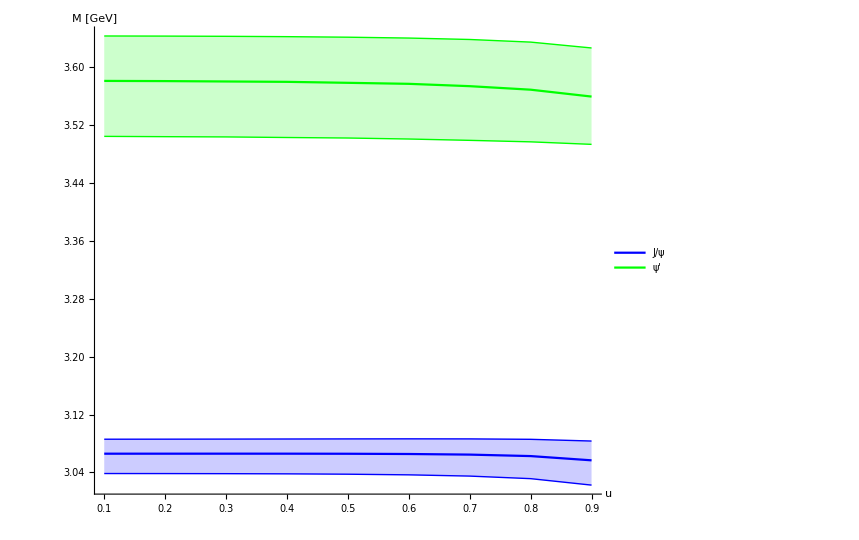

```mathematica
ListPlot[{Transpose[{uscan1[[;;]],wrfitcc1[[;;9,2]]}],Transpose[{uscan1[[;;]],wrfitcc1[[;;9,3]]}],Transpose[{uscan1[[;;]],wrfitcc1[[;;9,4]]}],Transpose[{uscan1[[;;]],wrfitcc2[[;;9,2]]}],Transpose[{uscan1[[;;]],wrfitcc2[[;;9,3]]}],Transpose[{uscan1[[;;]],wrfitcc2[[;;9,4]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.8,0.4}]]
```

```mathematica
Append[Transpose[{uscan1,gfitcc[[;;9,1]],gfitccu[[All,1]],gfitccl[[All,1]]}],{uscan[[10]],gfitcc[[10,1]]}]
```

{{1/10,0.0349207,0.0502821,0.0156337},{1/5,0.0353555,0.0507826,0.0158117},{3/10,0.0363197,0.0516168,0.0163177},{2/5,0.037269,0.0527632,0.0164763},{1/2,0.0384551,0.0543184,0.0170076},{3/5,0.0401772,0.0559847,0.0177189},{7/10,0.0423939,0.057771,0.0186402},{4/5,0.0451891,0.0596328,0.0198139},{9/10,0.0482354,0.0587281,0.0210906},{99/100,0.039689}}

```mathematica
gfit250cc1={{1/10,0.03492073173944248,0.05028212768851886,0.01563367470275798},{1/5,0.03535548066914216,0.050782593038717544,0.01581170217335914},{3/10,0.036319745540227474,0.05161680579336562,0.016317677192368495},{2/5,0.03726900839964086,0.05276322111165877,0.01647629015917203},{1/2,0.03845506344714222,0.054318448006032534,0.017007596484306192},{3/5,0.040177246572431935,0.055984717863657336,0.017718859146630978},{7/10,0.042393854586022295,0.05777095299106779,0.0186402059828873},{4/5,0.04518912069212665,0.05963277418474434,0.01981385031412365},{9/10,0.04823543513445174,0.05872813491656895,0.02109064566547072},{99/100,0.03968900276309511}};
```

```mathematica
gfit250cc1[[-1]]={gfit250cc1[[-1,1]],gfit250cc1[[-1,2]],gfit250cc1[[9,3]]/gfit250cc1[[9,2]] gfit250cc1[[-1,2]],gfit250cc1[[9,4]]/gfit250cc1[[9,2]] gfit250cc1[[-1,2]]};
```

```mathematica
gfit250cc1=gfit250cc1/.{a_,b_,c_,d_}:>{a,b+1/2(c-d),c,b}
```

{{1/10,0.03614,0.045509,0.02975},{1/5,0.0362947,0.0457028,0.0298233},{3/10,0.0365437,0.0460166,0.0299341},{2/5,0.0368637,0.04642,0.0300613},{1/2,0.0372139,0.0468608,0.0301665},{3/5,0.0375155,0.047245,0.0301742},{7/10,0.0375872,0.0473437,0.029931},{4/5,0.0369897,0.0466062,0.029074},{9/10,0.0342936,0.0432445,0.0264545},{99/100,0.0202181,0.0256015,0.0148966}}

```mathematica
gfitcc1inter=Interpolation[gfit250cc1[[All,;;2]],InterpolationOrder->1];
gfitcc1interl=Interpolation[gfit250cc1[[All,1;;3;;2]],InterpolationOrder->1];
gfitcc1interu=Interpolation[gfit250cc1[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitcc1inter[0],gfitcc1interl[0],gfitcc1interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.034486,0.0497817,0.0154556}

```mathematica
gfitcc1n=Join[{{0,0.034485982809742806,0.04978166233832018,0.015455647232156821}},gfit250cc1]
```

{{0,0.034486,0.0497817,0.0154556},{1/10,0.0349207,0.0502821,0.0156337},{1/5,0.0353555,0.0507826,0.0158117},{3/10,0.0363197,0.0516168,0.0163177},{2/5,0.037269,0.0527632,0.0164763},{1/2,0.0384551,0.0543184,0.0170076},{3/5,0.0401772,0.0559847,0.0177189},{7/10,0.0423939,0.057771,0.0186402},{4/5,0.0451891,0.0596328,0.0198139},{9/10,0.0482354,0.0587281,0.0210906},{99/100,0.039689,0.0483226,0.0173538}}

```mathematica
gfitcc1inter=Interpolation[gfitcc1n[[All,;;2]],InterpolationOrder->5];
gfitcc1interl=Interpolation[gfitcc1n[[All,1;;3;;2]],InterpolationOrder->5];
gfitcc1interu=Interpolation[gfitcc1n[[All,1;;4;;3]],InterpolationOrder->5];
```

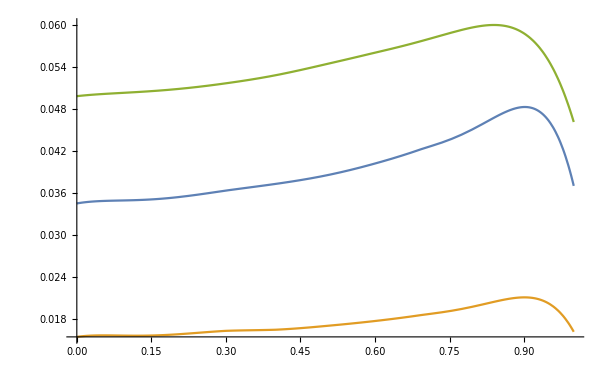

```mathematica
Plot[{gfitcc1inter[x],gfitcc1interu[x],gfitcc1interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/Jpsi_width_T150_perp.dat",Table[N[{u,gfitcc1inter[u],gfitcc1interu[u],gfitcc1interl[u]}],{u,0,1,1/20}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Jpsi_width_T150_perp.dat

```mathematica
Append[Transpose[{uscan1,gfitcc[[;;9,2]],gfitccu[[All,2]],gfitccl[[All,2]]}],{uscan[[10]],gfitcc[[10,2]]}]
```

{{1/10,0.174826,0.235068,0.0925935},{1/5,0.176113,0.236798,0.0932222},{3/10,0.178759,0.24022,0.0944241},{2/5,0.181908,0.244449,0.0956275},{1/2,0.186061,0.250271,0.0972674},{3/5,0.190912,0.256009,0.0992537},{7/10,0.196371,0.261627,0.1013},{4/5,0.201249,0.265594,0.10284},{9/10,0.200294,0.257627,0.101273},{99/100,0.140787}}

```mathematica
gfit250cc2={{1/10,0.17482604026948695,0.23506815868830158,0.0925934811875465},{1/5,0.17611266945922813,0.2367984605475298,0.09322216404649034},{3/10,0.17875944892637666,0.24021977257075633,0.0944240974189367},{2/5,0.1819084447374736,0.2444490613945457,0.09562753981268199},{1/2,0.1860605840884383,0.25027124439436477,0.09726741253635368},{3/5,0.19091221403709013,0.2560093134353526,0.09925365028299737},{7/10,0.19637084852103184,0.26162662824628913,0.1013004021787059},{4/5,0.20124934079637163,0.26559435497660094,0.10284017703084432},{9/10,0.20029423487175477,0.25762658112088427,0.10127276148205613},{99/100,0.14078654284496292}};
```

```mathematica
gfit250cc2[[-1]]={gfit250cc2[[-1,1]],gfit250cc2[[-1,2]],gfit250cc2[[9,3]]/gfit250cc2[[9,2]] gfit250cc2[[-1,2]],gfit250cc2[[9,4]]/gfit250cc2[[9,2]] gfit250cc2[[-1,2]]};
```

```mathematica
gfitcc1inter=Interpolation[gfit250cc2[[All,;;2]],InterpolationOrder->1];
gfitcc1interl=Interpolation[gfit250cc2[[All,1;;3;;2]],InterpolationOrder->1];
gfitcc1interu=Interpolation[gfit250cc2[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitcc1inter[0],gfitcc1interl[0],gfitcc1interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.173539,0.233338,0.0919648}

```mathematica
gfitcc2n=Join[{{0,0.17353941107974577,0.23333785682907338,0.09196479832860266}},gfit250cc2]
```

{{0,0.173539,0.233338,0.0919648},{1/10,0.174826,0.235068,0.0925935},{1/5,0.176113,0.236798,0.0932222},{3/10,0.178759,0.24022,0.0944241},{2/5,0.181908,0.244449,0.0956275},{1/2,0.186061,0.250271,0.0972674},{3/5,0.190912,0.256009,0.0992537},{7/10,0.196371,0.261627,0.1013},{4/5,0.201249,0.265594,0.10284},{9/10,0.200294,0.257627,0.101273},{99/100,0.140787,0.181085,0.0711845}}

```mathematica
gfitcc2inter=Interpolation[gfitcc2n[[All,;;2]],InterpolationOrder->5];
gfitcc2interl=Interpolation[gfitcc2n[[All,1;;3;;2]],InterpolationOrder->5];
gfitcc2interu=Interpolation[gfitcc2n[[All,1;;4;;3]],InterpolationOrder->5];
```

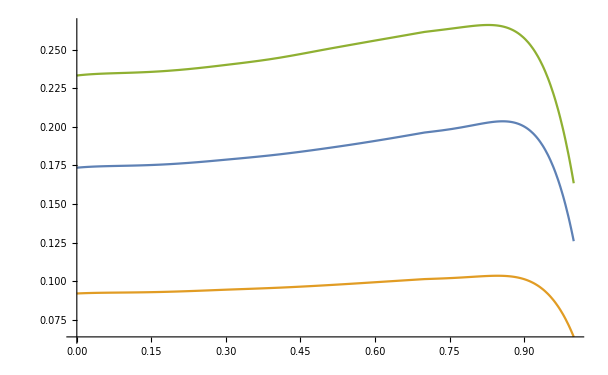

```mathematica
Plot[{gfitcc2inter[x],gfitcc2interu[x],gfitcc2interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/psip_width_T150_perp.dat",Table[N[{u,gfitcc2inter[u],gfitcc2interu[u],gfitcc2interl[u]}],{u,0,1,1/20}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/psip_width_T150_perp.dat

#### Bottomonium Tc Perpendicular

```mathematica
Do[bbdata[n]=Import["bb_perp/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectra.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[bbdatau[n]=Import["bb_perp/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectrau.dat"];,{n,Length[uscan1]}];
```

```mathematica
Do[bbdatal[n]=Import["bb_perp/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectral.dat"];,{n,Length[uscan1]}];
```

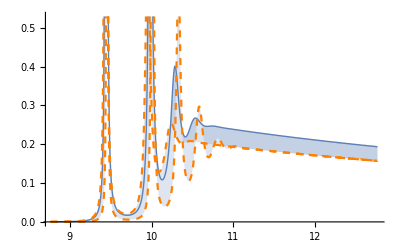

```mathematica
Block[{n=1},ListPlot[{bbdata[n],bbdatal[n],bbdatau[n]},Joined->True,Filling->{1->{2},1->{3}},PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[bbmodelu,bbmodell,bbmodel]
Quiet[fit[bbdata,bbmodel,uscanI]];
Quiet[fit[bbdatal,bbmodell,uscanI1]];
Quiet[fit[bbdatau,bbmodelu,uscanI1]];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[wr,wrfitbbl,bbmodell];
store[wr,wrfitbbu,bbmodelu];
store[Γ,gfitbb,bbmodel];
store[Γ,gfitbbl,bbmodell];
store[Γ,gfitbbu,bbmodelu];
store[const,cfitbb,bbmodel];
store[const,cfitbbl,bbmodell];
store[const,cfitbbu,bbmodelu];
store[δbg,dfitbb,bbmodel];
store[δbg,dfitbbl,bbmodell];
store[δbg,dfitbbu,bbmodelu];
store[shift,sfitbb,bbmodel];
store[shift,sfitbbl,bbmodell];
store[shift,sfitbbu,bbmodelu];
store[shift2,s2fitbb,bbmodel];
store[shift2,s2fitbbl,bbmodell];
store[shift2,s2fitbbu,bbmodelu];
storearea[areafitbb,bbmodel];
storearea[areafitbbl,bbmodell];
storearea[areafitbbu,bbmodelu];
```

```mathematica
Append[Transpose[{uscan1,wrfitbb[[;;9,1]],wrfitbbu[[All,1]],wrfitbbl[[All,1]]}],{uscan[[10]],wrfitbb[[10,1]]}]
```

{{1/10,9.44454,9.4373,9.456},{1/5,9.44474,9.43752,9.45614},{3/10,9.44506,9.43787,9.45638},{2/5,9.44551,9.43834,9.45671},{1/2,9.44606,9.43887,9.45714},{3/5,9.44666,9.43938,9.45764},{7/10,9.4472,9.43963,9.45819},{4/5,9.44732,9.43899,9.45866},{9/10,9.44551,9.4348,9.45844},{99/100,9.42354}}

```mathematica
wrfitbb1={{1/10,9.444536013582654,9.437297757519659,9.455998163591516},{1/5,9.444735595345085,9.437517088263046,9.456140993132054},{3/10,9.445064095871812,9.437871186801871,9.45638045385252},{2/5,9.445512433827835,9.438338792568397,9.456713601938072},{1/2,9.446059977613972,9.438874451572392,9.457138428987621},{3/5,9.44666178466053,9.439382343419261,9.457642600942757},{7/10,9.447199948792985,9.439634392826967,9.458190284007106},{4/5,9.44732307834871,9.438986571521584,9.458656144914746},{9/10,9.445511369802041,9.434800289275596,9.458444076156203},{99/100,9.423535041316958}};
```

```mathematica
wrfitbb1[[-1]]={wrfitbb1[[-1,1]],wrfitbb1[[-1,2]],wrfitbb1[[9,3]]/wrfitbb1[[9,2]] wrfitbb1[[-1,2]],wrfitbb1[[9,4]]/wrfitbb1[[9,2]] wrfitbb1[[-1,2]]};
wrfitbb1inter=Interpolation[wrfitbb1[[All,;;2]],InterpolationOrder->1];
wrfitbb1interl=Interpolation[wrfitbb1[[All,1;;3;;2]],InterpolationOrder->1];
wrfitbb1interu=Interpolation[wrfitbb1[[All,1;;4;;3]],InterpolationOrder->1];
Export["final/Upsilon1_mass_T150_perp.dat",Quiet[N[Join[{{0,wrfitbb1inter[0],wrfitbb1interl[0],wrfitbb1interu[0]}},wrfitbb1]]]]
```

final/Upsilon1_mass_T150_perp.dat

```mathematica
Append[Transpose[{uscan1,wrfitbb[[;;9,2]],wrfitbbu[[All,2]],wrfitbbl[[All,2]]}],{uscan[[10]],wrfitbb[[10,2]]}]
```

{{1/10,9.98253,9.94938,10.009},{1/5,9.98247,9.94921,10.009},{3/10,9.98237,9.94889,10.0091},{2/5,9.98215,9.94834,10.0091},{1/2,9.98176,9.94749,10.0091},{3/5,9.98104,9.94602,10.009},{7/10,9.97964,9.94358,10.0087},{4/5,9.97673,9.93896,10.0076},{9/10,9.96934,9.92858,10.0043},{99/100,9.93859}}

```mathematica
wrfitbb2={{1/10,9.982527168218894,9.949382275404897,10.008969992309932},{1/5,9.982474123731995,9.949208420740657,10.009005396839296},{3/10,9.982365484820289,9.948890141956193,10.009054622002914},{2/5,9.98215441069633,9.948335249945599,10.009100457958942},{1/2,9.981762410253499,9.947487926737805,10.009108597268142},{3/5,9.98103765639555,9.94602395418376,10.00901201280823},{7/10,9.979637211773918,9.9435759428101,10.008657319327924},{4/5,9.976733484136059,9.938960383827538,10.007632413992408},{9/10,9.969339067521709,9.928583907417481,10.004342199601213},{99/100,9.938592141588382}};
```

```mathematica
wrfitbb2[[-1]]={wrfitbb2[[-1,1]],wrfitbb2[[-1,2]],wrfitbb2[[9,3]]/wrfitbb2[[9,2]] wrfitbb2[[-1,2]],wrfitbb2[[9,4]]/wrfitbb2[[9,2]] wrfitbb2[[-1,2]]};
wrfitbb2inter=Interpolation[wrfitbb2[[All,;;2]],InterpolationOrder->1];
wrfitbb2interl=Interpolation[wrfitbb2[[All,1;;3;;2]],InterpolationOrder->1];
wrfitbb2interu=Interpolation[wrfitbb2[[All,1;;4;;3]],InterpolationOrder->1];
Export["final/Upsilon2_mass_T150_perp.dat",Quiet[N[Join[{{0,wrfitbb2inter[0],wrfitbb2interl[0],wrfitbb2interu[0]}},wrfitbb2]]]]
```

final/Upsilon2_mass_T150_perp.dat

```mathematica
Append[Transpose[{uscan1,wrfitbb[[;;9,3]],wrfitbbu[[All,3]],wrfitbbl[[All,3]]}],{uscan[[10]],wrfitbb[[10,3]]}]
```

{{1/10,10.2762,10.214,10.3268},{1/5,10.276,10.2135,10.3267},{3/10,10.2791,10.2128,10.3265},{2/5,10.2743,10.2126,10.3262},{1/2,10.2733,10.2124,10.3257},{3/5,10.2753,10.2096,10.3248},{7/10,10.2688,10.2074,10.3234},{4/5,10.2634,10.2025,10.3206},{9/10,10.2534,10.194,10.314},{99/100,10.2322}}

```mathematica
wrfitbb3={{1/10,10.2761864408688,10.213954153099976,10.326779035365751},{1/5,10.27601961383375,10.213517627748283,10.326692013212531},{3/10,10.279126312712979,10.212771116725948,10.326503007449089},{2/5,10.274254752294961,10.212580827831435,10.326176809211397},{1/2,10.273272674526801,10.212432142329328,10.32567792636185},{3/5,10.275277220764979,10.20963637770643,10.32484486420711},{7/10,10.26877054008348,10.207430559126111,10.323407351030397},{4/5,10.263376470724117,10.20250384485756,10.320636994282639},{9/10,10.253438958510655,10.19401000812573,10.314039173771455},{99/100,10.232240173858978}};
```

```mathematica
wrfitbb3[[-1]]={wrfitbb3[[-1,1]],wrfitbb3[[-1,2]],wrfitbb3[[9,3]]/wrfitbb3[[9,2]] wrfitbb3[[-1,2]],wrfitbb3[[9,4]]/wrfitbb3[[9,2]] wrfitbb3[[-1,2]]};
wrfitbb3inter=Interpolation[wrfitbb3[[All,;;2]],InterpolationOrder->1];
wrfitbb3interl=Interpolation[wrfitbb3[[All,1;;3;;2]],InterpolationOrder->1];
wrfitbb3interu=Interpolation[wrfitbb3[[All,1;;4;;3]],InterpolationOrder->1];
Export["final/Upsilon3_mass_T150_perp.dat",Quiet[N[Join[{{0,wrfitbb3inter[0],wrfitbb3interl[0],wrfitbb3interu[0]}},wrfitbb3]]]]
```

final/Upsilon3_mass_T150_perp.dat

```mathematica
Append[Transpose[{uscan1,gfitbb[[;;9,1]],gfitbbu[[All,1]],gfitbbl[[All,1]]}],{uscan[[10]],gfitbb[[10,1]]}]
```

{{1/10,0.00735038,0.0112024,0.00310006},{1/5,0.00749223,0.011352,0.00316015},{3/10,0.007916,0.0116047,0.00335339},{2/5,0.0080747,0.0119574,0.00338238},{1/2,0.00848569,0.0124487,0.00357973},{3/5,0.0091214,0.01299,0.0038593},{7/10,0.0100263,0.013608,0.00426446},{4/5,0.0113724,0.014316,0.00488819},{9/10,0.0135334,0.0145708,0.005928},{99/100,0.0147324}}

```mathematica
gfit250bb1={{1/10,0.0073503788567403855,0.011202413442696423,0.0031000586702140754},{1/5,0.007492233673102118,0.01135198803691136,0.003160147506147531},{3/10,0.00791600217092206,0.011604702459742619,0.003353393158426751},{2/5,0.008074698534648036,0.011957360691862127,0.0033823830349987245},{1/2,0.008485685123642374,0.012448735291525603,0.003579728581967443},{3/5,0.009121402452273627,0.012990013757498413,0.003859300505224648},{7/10,0.010026266912017329,0.013607989886740392,0.004264464956883984},{4/5,0.011372373843507241,0.014316046138213199,0.004888193144456682},{9/10,0.013533444356343358,0.014570792002737329,0.005928004031747936},{99/100,0.0147323903158994}};
```

```mathematica
gfit250bb1[[-1]]={gfit250bb1[[-1,1]],gfit250bb1[[-1,2]],gfit250bb1[[9,3]]/gfit250bb1[[9,2]] gfit250bb1[[-1,2]],gfit250bb1[[9,4]]/gfit250bb1[[9,2]] gfit250bb1[[-1,2]]};
```

```mathematica
gfit250bb1=gfit250bb1/.{a_,b_,c_,d_}:>{a,b,gfit250bb1[[1,3]]-gfit250bb1[[1,2]]+b,d};
```

```mathematica
gfitcc1inter=Interpolation[gfit250bb1[[All,;;2]],InterpolationOrder->1];
gfitcc1interl=Interpolation[gfit250bb1[[All,1;;3;;2]],InterpolationOrder->1];
gfitcc1interu=Interpolation[gfit250bb1[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitcc1inter[0],gfitcc1interl[0],gfitcc1interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.00720852,0.0110606,0.00303997}

```mathematica
gfitbb1n=Join[{{0,0.007208524040378653,0.01106055862633469,0.00303996983428062}},gfit250bb1]
```

{{0,0.00720852,0.0110606,0.00303997},{1/10,0.00735038,0.0112024,0.00310006},{1/5,0.00749223,0.0113443,0.00316015},{3/10,0.007916,0.011768,0.00335339},{2/5,0.0080747,0.0119267,0.00338238},{1/2,0.00848569,0.0123377,0.00357973},{3/5,0.0091214,0.0129734,0.0038593},{7/10,0.0100263,0.0138783,0.00426446},{4/5,0.0113724,0.0152244,0.00488819},{9/10,0.0135334,0.0173855,0.005928},{99/100,0.0147324,0.0185844,0.00645317}}

```mathematica
gfitbb1inter=Interpolation[gfitbb1n[[All,;;2]],InterpolationOrder->5];
gfitbb1interl=Interpolation[gfitbb1n[[All,1;;3;;2]],InterpolationOrder->5];
gfitbb1interu=Interpolation[gfitbb1n[[All,1;;4;;3]],InterpolationOrder->5];
```

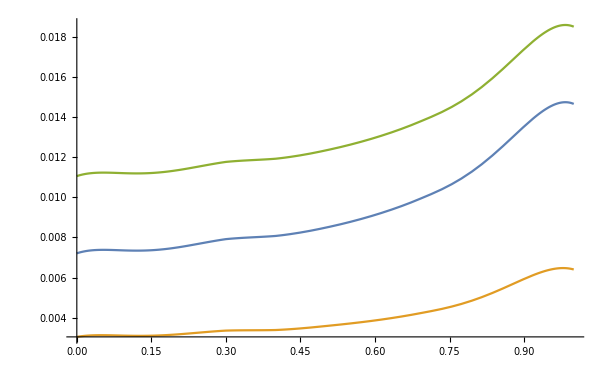

```mathematica
Plot[{gfitbb1inter[x],gfitbb1interu[x],gfitbb1interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/Upsilon1_width_T150_perp.dat",Table[N[{u,gfitbb1inter[u],gfitbb1interu[u],gfitbb1interl[u]}],{u,0,1,1/20}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Upsilon1_width_T150_perp.dat

```mathematica
Append[Transpose[{uscan1,gfitbb[[;;9,2]],gfitbbu[[All,2]],gfitbbl[[All,2]]}],{uscan[[10]],gfitbb[[10,2]]}]
```

{{1/10,0.0471611,0.0672473,0.0213498},{1/5,0.0477011,0.0678711,0.0215757},{3/10,0.0488109,0.0688551,0.0221693},{2/5,0.0500945,0.0702827,0.0224186},{1/2,0.051566,0.0720571,0.0230747},{3/5,0.053608,0.0740868,0.0239398},{7/10,0.0561872,0.0760432,0.025021},{4/5,0.0592728,0.0781646,0.0263087},{9/10,0.0622194,0.0765677,0.027458},{99/100,0.0492163}}

```mathematica
gfit250bb2={{1/10,0.047161062240495905,0.0672472924789864,0.021349756990694562},{1/5,0.04770110085011129,0.06787106582662814,0.021575658376731307},{3/10,0.04881089694853506,0.06885509185083433,0.022169302138405133},{2/5,0.05009448574838259,0.07028271151325041,0.022418581127391757},{1/2,0.051566033435616124,0.07205707839511447,0.023074740030865574},{3/5,0.05360795434543074,0.07408676787072872,0.023939808556549216},{7/10,0.05618720931914954,0.07604316197601639,0.025021015689643093},{4/5,0.05927282754864275,0.07816461675763785,0.026308685527493308},{9/10,0.06221937371357773,0.07656772472488395,0.02745800194069238},{99/100,0.04921626609159239}};
```

```mathematica
gfit250bb2[[-1]]={gfit250bb2[[-1,1]],gfit250bb2[[-1,2]],gfit250bb2[[9,3]]/gfit250bb2[[9,2]] gfit250bb2[[-1,2]],gfit250bb2[[9,4]]/gfit250bb2[[9,2]] gfit250bb2[[-1,2]]};
```

```mathematica
gfit250bb2=gfit250bb2/.{a_,b_,c_,d_}:>{a,b,gfit250bb2[[1,3]]-gfit250bb2[[1,2]]+b,d};
```

```mathematica
gfitcc2inter=Interpolation[gfit250bb2[[All,;;2]],InterpolationOrder->1];
gfitcc2interl=Interpolation[gfit250bb2[[All,1;;3;;2]],InterpolationOrder->1];
gfitcc2interu=Interpolation[gfit250bb2[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitcc2inter[0],gfitcc2interl[0],gfitcc2interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.046621,0.0666235,0.0211239}

```mathematica
gfitbb2n=Join[{{0,0.04662102363088052,0.06662351913134468,0.021123855604657817}},gfit250bb2]
```

{{0,0.046621,0.0666235,0.0211239},{1/10,0.0471611,0.0672473,0.0213498},{1/5,0.0477011,0.0678711,0.0215757},{3/10,0.0488109,0.0688551,0.0221693},{2/5,0.0500945,0.0702827,0.0224186},{1/2,0.051566,0.0720571,0.0230747},{3/5,0.053608,0.0740868,0.0239398},{7/10,0.0561872,0.0760432,0.025021},{4/5,0.0592728,0.0781646,0.0263087},{9/10,0.0622194,0.0765677,0.027458},{99/100,0.0492163,0.060566,0.0217196}}

```mathematica
gfitbb2inter=Interpolation[gfitbb2n[[All,;;2]],InterpolationOrder->5];
gfitbb2interl=Interpolation[gfitbb2n[[All,1;;3;;2]],InterpolationOrder->5];
gfitbb2interu=Interpolation[gfitbb2n[[All,1;;4;;3]],InterpolationOrder->5];
```

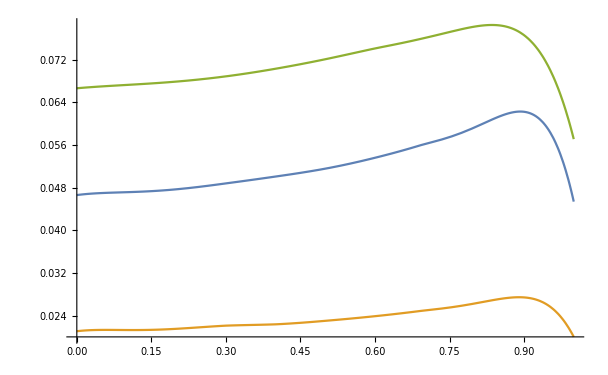

```mathematica
Plot[{gfitbb2inter[x],gfitbb2interu[x],gfitbb2interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/Upsilon2_width_T150_perp.dat",Table[N[{u,gfitbb2inter[u],gfitbb2interu[u],gfitbb2interl[u]}],{u,0,1,1/20}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Upsilon2_width_T150_perp.dat

```mathematica
Append[Transpose[{uscan1,gfitbb[[;;9,3]],gfitbbu[[All,3]],gfitbbl[[All,3]]}],{uscan[[10]],gfitbb[[10,3]]}]
```

{{1/10,0.115261,0.149561,0.0606799},{1/5,0.116217,0.150715,0.0610538},{3/10,0.112596,0.151954,0.0619796},{2/5,0.120518,0.154489,0.0627317},{1/2,0.122698,0.155533,0.0638202},{3/5,0.120513,0.160142,0.0651597},{7/10,0.129408,0.163027,0.0666093},{4/5,0.132189,0.165282,0.0678339},{9/10,0.132501,0.162783,0.0674592},{99/100,0.0972556}}

```mathematica
gfit250bb3={{1/10,0.11526137624664409,0.14956112495895083,0.06067987178246919},{1/5,0.11621736158050756,0.15071467379617454,0.06105378273002951},{3/10,0.11259624555090185,0.15195444665866903,0.06197959380168095},{2/5,0.12051837155203285,0.1544889338673654,0.06273174688187003},{1/2,0.12269767299674451,0.15553329297430085,0.06382015362405792},{3/5,0.12051254093080105,0.160141973991899,0.06515972980950029},{7/10,0.1294082512067042,0.163027298767094,0.06660931539815283},{4/5,0.13218899912833085,0.1652819768450232,0.0678339069526542},{9/10,0.1325005899737765,0.16278310015556238,0.06745915393211285},{99/100,0.09725564453510097}};
```

```mathematica
gfit250bb3[[-1]]={gfit250bb3[[-1,1]],gfit250bb3[[-1,2]],gfit250bb3[[9,3]]/gfit250bb3[[9,2]] gfit250bb3[[-1,2]],gfit250bb3[[9,4]]/gfit250bb3[[9,2]] gfit250bb3[[-1,2]]};
```

```mathematica
gfit250bb3=gfit250bb3/.{a_,b_,c_,d_}:>{a,b,gfit250bb3[[1,3]]-gfit250bb3[[1,2]]+b,d};
```

```mathematica
gfitcc3inter=Interpolation[gfit250bb3[[All,;;2]],InterpolationOrder->1];
gfitcc3interl=Interpolation[gfit250bb3[[All,1;;3;;2]],InterpolationOrder->1];
gfitcc3interu=Interpolation[gfit250bb3[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitcc3inter[0],gfitcc3interl[0],gfitcc3interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.114305,0.148408,0.060306}

```mathematica
gfitbb3n=Join[{{0,0.11430539091278062,0.14840757612172711,0.06030596083490887}},gfit250bb3]
```

{{0,0.114305,0.148408,0.060306},{1/10,0.115261,0.149561,0.0606799},{1/5,0.116217,0.150715,0.0610538},{3/10,0.112596,0.151954,0.0619796},{2/5,0.120518,0.154489,0.0627317},{1/2,0.122698,0.155533,0.0638202},{3/5,0.120513,0.160142,0.0651597},{7/10,0.129408,0.163027,0.0666093},{4/5,0.132189,0.165282,0.0678339},{9/10,0.132501,0.162783,0.0674592},{99/100,0.0972556,0.119483,0.0495151}}

```mathematica
gfitbb3inter=Interpolation[gfitbb3n[[All,;;2]],InterpolationOrder->5];
gfitbb3interl=Interpolation[gfitbb3n[[All,1;;3;;2]],InterpolationOrder->5];
gfitbb3interu=Interpolation[gfitbb3n[[All,1;;4;;3]],InterpolationOrder->5];
```

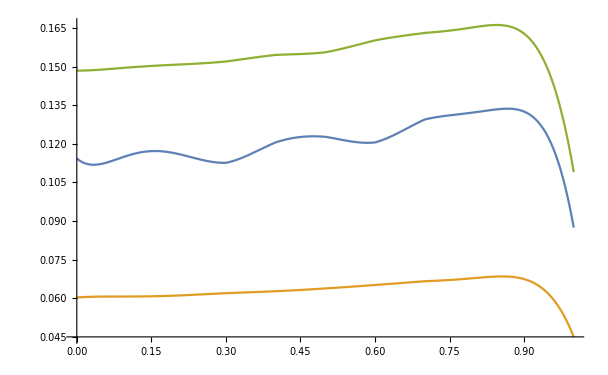

```mathematica
Plot[{gfitbb3inter[x],gfitbb3interu[x],gfitbb3interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/Upsilon3_width_T150_perp.dat",Table[N[{u,gfitbb3inter[u],gfitbb3interu[u],gfitbb3interl[u]}],{u,0,1,1/20}]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/Upsilon3_width_T150_perp.dat

#### Charmonium 250 MeV Perpendicular

```mathematica
Do[ccdata[n]=Import["cc_perp/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250.dat"];,{n,Length[uscan]}];
```

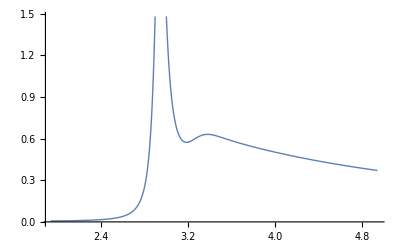

```mathematica
Block[{n=1},ListPlot[{ccdata[n]},Joined->True,PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata,ccmodel,uscanI]];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[Γ,gfitcc,ccmodel];
store[const,cfitcc,ccmodel];
store[δbg,dfitcc,ccmodel];
store[shift,sfitcc,ccmodel];
store[shift2,s2fitcc,ccmodel];
storearea[areafitcc,ccmodel];
```

```mathematica
Transpose[{uscan,wrfitcc[[All,1]]}]
```

{{1/10,2.9376},{1/5,2.93737},{3/10,2.93698},{2/5,2.93632},{1/2,2.93526},{3/5,2.9336},{7/10,2.93081},{4/5,2.92567},{9/10,2.91427},{99/100,2.87312}}

```mathematica
wrfit250cc1={{1/10,2.9375987865344735},{1/5,2.9373727994838763},{3/10,2.93697677044667},{2/5,2.936317054533937},{1/2,2.9352613819680777},{3/5,2.9336001617095775},{7/10,2.9308079929532225},{4/5,2.925673107546299},{9/10,2.9142655732229903},{99/100,2.8731160670275204}};
```

```mathematica
up=1.0194037213198428;
```

```mathematica
low=0.9789039593655589;
```

```mathematica
Do[wrfit250cc1[[i]]=Append[Append[wrfit250cc1[[i]],up wrfit250cc1[[i,2]]],low wrfit250cc1[[i,2]]],{i,Length[wrfit250cc1]}]
```

```mathematica
wrfit250cc1
```

{{1/10,2.9376,2.9946,2.87563},{1/5,2.93737,2.99437,2.87541},{3/10,2.93698,2.99397,2.87502},{2/5,2.93632,2.99329,2.87437},{1/2,2.93526,2.99222,2.87334},{3/5,2.9336,2.99052,2.87171},{7/10,2.93081,2.98768,2.86898},{4/5,2.92567,2.98244,2.86395},{9/10,2.91427,2.97081,2.85279},{99/100,2.87312,2.92887,2.8125}}

```mathematica
wrfit250cc1inter=Interpolation[wrfit250cc1[[All,;;2]],InterpolationOrder->1];
wrfit250cc1interl=Interpolation[wrfit250cc1[[All,1;;3;;2]],InterpolationOrder->1];
wrfit250cc1interu=Interpolation[wrfit250cc1[[All,1;;4;;3]],InterpolationOrder->1];
Export["final/data/Jpsi_mass_T250_perp.dat",N[Join[{{0,wrfit250cc1inter[0],wrfit250cc1interl[0],wrfit250cc1interu[0]}},wrfit250cc1]]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/data/Jpsi_mass_T250_perp.dat

```mathematica
gfitbb1inter=Interpolation[gfit250bb1[[All,;;2]],InterpolationOrder->1];
gfitbb1interl=Interpolation[gfit250bb1[[All,1;;3;;2]],InterpolationOrder->1];
gfitbb1interu=Interpolation[gfit250bb1[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitbb1inter[0],gfitbb1interl[0],gfitbb1interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.0263788,0.0217147,0.0332173}

```mathematica
gfitbb1n=Join[{{0,0.026378819125579066,0.02171471326122529,0.03321730475593329}},gfit250bb1]
```

{{0,0.0263788,0.0217147,0.0332173},{1/10,0.0266438,0.0219329,0.033551},{1/5,0.0269088,0.022151,0.0338847},{3/10,0.0274209,0.0225725,0.0345295},{2/5,0.0279978,0.0230474,0.0352559},{1/2,0.0287863,0.0236965,0.0362489},{3/5,0.0297345,0.0244771,0.037443},{7/10,0.030781,0.0253385,0.0387607},{4/5,0.0317525,0.0261383,0.0399841},{9/10,0.0318038,0.0261805,0.0400486},{99/100,0.0425151,0.0349979,0.0535368}}

```mathematica
gfitbb1inter=Interpolation[gfitbb1n[[All,;;2]],InterpolationOrder->5];
gfitbb1interl=Interpolation[gfitbb1n[[All,1;;3;;2]],InterpolationOrder->5];
gfitbb1interu=Interpolation[gfitbb1n[[All,1;;4;;3]],InterpolationOrder->5];
```

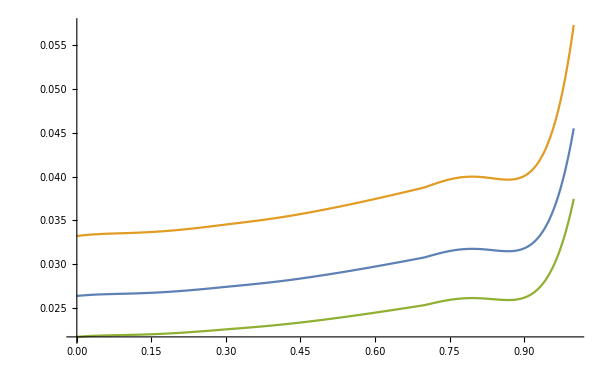

```mathematica
Plot[{gfitbb1inter[x],gfitbb1interu[x],gfitbb1interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/data/Upsilon1_width_T250_perp.dat",N[Table[{u,gfitbb1inter[u],gfitbb1interu[u],gfitbb1interl[u]},{u,0,1,1/20}]]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/data/Upsilon1_width_T250_perp.dat

```mathematica
Transpose[{uscan,wrfitcc[[All,2]]}]
```

{{1/10,3.26641},{1/5,3.26724},{3/10,3.26893},{2/5,3.27099},{1/2,3.27347},{3/5,3.27646},{7/10,3.27924},{4/5,3.28148},{9/10,3.29936},{99/100,3.35235}}

```mathematica
Transpose[{uscan,gfitcc[[All,2]]}]
```

{{1/10,0.337092},{1/5,0.338562},{3/10,0.340087},{2/5,0.342646},{1/2,0.346551},{3/5,0.349896},{7/10,0.354585},{4/5,0.358377},{9/10,0.361335},{99/100,0.303522}}

```mathematica
(*gfit250cc1=gfit250cc10/.{a_,b_,c_,d_}:>{a,b,c,b-(c-b)}*)
```

#### Bottomonium 250 MeV Perpendicular

```mathematica
Do[bbdata2[n]=Import["bb_perp/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250.dat"];,{n,Length[uscan]}];
```

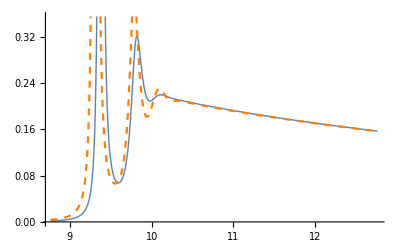

```mathematica
Block[{n=9},ListPlot[{bbdata2[n],bbdata2[n+1]},Joined->True,PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
uscan10={99/100}
```

{99/100}

```mathematica
Clear[bbmodelu,bbmodell,bbmodel]
Quiet[fit[bbdata2,bbmodel,uscan10]];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[Γ,gfitbb,bbmodel];
store[const,cfitbb,bbmodel];
store[δbg,dfitbb,bbmodel];
store[shift,sfitbb,bbmodel];
store[shift2,s2fitbb,bbmodel];
storearea[areafitbb,bbmodel];
```

```mathematica
Transpose[{uscan,wrfitbb[[All,1]]}]
```

{{1/10,9.39269},{1/5,9.39284},{3/10,9.39307},{2/5,9.3933},{1/2,9.39341},{3/5,9.39315},{7/10,9.39194},{4/5,9.38833},{9/10,9.3768},{99/100,9.31061}}

```mathematica
wrfit250bb1={{1/10,9.392685471099584},{1/5,9.392842886396108},{3/10,9.393071518005254},{2/5,9.393302669173524},{1/2,9.39341188299078},{3/5,9.393145512074506},{7/10,9.391943315941214},{4/5,9.388330242761127},{9/10,9.37680237084617},{99/100,9.310611547159205}};
```

```mathematica
low=9.362547491966819/9.393104687961864
```

0.996747

```mathematica
up=9.41923794150853/9.393104687961864
```

1.00278

```mathematica
Do[wrfit250bb1[[i]]=Append[Append[wrfit250bb1[[i]],low wrfit250bb1[[i,2]]],up wrfit250bb1[[i,2]]],{i,Length[wrfit250bb1]}]
```

```mathematica
wrfit250bb1
```

{{1/10,9.39269,9.36213,9.41882},{1/5,9.39284,9.36229,9.41898},{3/10,9.39307,9.36251,9.4192},{2/5,9.3933,9.36274,9.41944},{1/2,9.39341,9.36285,9.41955},{3/5,9.39315,9.36259,9.41928},{7/10,9.39194,9.36139,9.41807},{4/5,9.38833,9.35779,9.41445},{9/10,9.3768,9.3463,9.40289},{99/100,9.31061,9.28032,9.33652}}

```mathematica
wrfitbb1inter=Interpolation[wrfit250bb1[[All,;;2]],InterpolationOrder->1];
wrfitbb1interl=Interpolation[wrfit250bb1[[All,1;;3;;2]],InterpolationOrder->1];
wrfitbb1interu=Interpolation[wrfit250bb1[[All,1;;4;;3]],InterpolationOrder->1];
Export["final/data/Upsilon1_mass_T250_perp.dat",N[Join[{{0,wrfitbb1inter[0],wrfitbb1interl[0],wrfitbb1interu[0]}},wrfit250bb1]]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/data/Upsilon1_mass_T250_perp.dat

```mathematica
Transpose[{uscan,gfitbb[[All,1]]}]
```

{{1/10,0.0266438},{1/5,0.0269088},{3/10,0.0274209},{2/5,0.0279978},{1/2,0.0287863},{3/5,0.0297345},{7/10,0.030781},{4/5,0.0317525},{9/10,0.0318038},{99/100,0.0425151}}

```mathematica
gfit250bb1={{1/10,0.02664381334670465},{1/5,0.026908807567830234},{3/10,0.0274208531339508},{2/5,0.027997750929785126},{1/2,0.02878629648651309},{3/5,0.029734538749995727},{7/10,0.030780995886430226},{4/5,0.03175249251875423},{9/10,0.031803786096425486},{99/100,0.04251507746217825}};
```

```mathematica
up=0.04550897431680757/0.03613998820537241
```

1.25924

```mathematica
low=0.0297499852972095/0.03613998820537241
```

0.823187

```mathematica
Do[gfit250bb1[[i]]=Append[Append[gfit250bb1[[i]],low gfit250bb1[[i,2]]],up gfit250bb1[[i,2]]],{i,Length[gfit250bb1]}]
```

```mathematica
gfit250bb1
```

{{1/10,0.0266438,0.0219329,0.033551},{1/5,0.0269088,0.022151,0.0338847},{3/10,0.0274209,0.0225725,0.0345295},{2/5,0.0279978,0.0230474,0.0352559},{1/2,0.0287863,0.0236965,0.0362489},{3/5,0.0297345,0.0244771,0.037443},{7/10,0.030781,0.0253385,0.0387607},{4/5,0.0317525,0.0261383,0.0399841},{9/10,0.0318038,0.0261805,0.0400486},{99/100,0.0425151,0.0349979,0.0535368}}

```mathematica
gfitbb1inter=Interpolation[gfit250bb1[[All,;;2]],InterpolationOrder->1];
gfitbb1interl=Interpolation[gfit250bb1[[All,1;;3;;2]],InterpolationOrder->1];
gfitbb1interu=Interpolation[gfit250bb1[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitbb1inter[0],gfitbb1interl[0],gfitbb1interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.0263788,0.0217147,0.0332173}

```mathematica
gfitbb1n=Join[{{0,0.026378819125579066,0.02171471326122529,0.03321730475593329}},gfit250bb1]
```

{{0,0.0263788,0.0217147,0.0332173},{1/10,0.0266438,0.0219329,0.033551},{1/5,0.0269088,0.022151,0.0338847},{3/10,0.0274209,0.0225725,0.0345295},{2/5,0.0279978,0.0230474,0.0352559},{1/2,0.0287863,0.0236965,0.0362489},{3/5,0.0297345,0.0244771,0.037443},{7/10,0.030781,0.0253385,0.0387607},{4/5,0.0317525,0.0261383,0.0399841},{9/10,0.0318038,0.0261805,0.0400486},{99/100,0.0425151,0.0349979,0.0535368}}

```mathematica
gfitbb1inter=Interpolation[gfitbb1n[[All,;;2]],InterpolationOrder->5];
gfitbb1interl=Interpolation[gfitbb1n[[All,1;;3;;2]],InterpolationOrder->5];
gfitbb1interu=Interpolation[gfitbb1n[[All,1;;4;;3]],InterpolationOrder->5];
```

```mathematica
Plot[{gfitbb1inter[x],gfitbb1interu[x],gfitbb1interl[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Export["final/data/Upsilon1_width_T250_perp.dat",N[Table[{u,gfitbb1inter[u],gfitbb1interu[u],gfitbb1interl[u]},{u,0,1,1/20}]]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/data/Upsilon1_width_T250_perp.dat

```mathematica
Transpose[{uscan,wrfitbb[[All,2]]}]
```

{{1/10,9.81918},{1/5,9.81865},{3/10,9.81809},{2/5,9.81717},{1/2,9.81569},{3/5,9.81346},{7/10,9.81052},{4/5,9.80591},{9/10,9.79777},{99/100,9.77642}}

```mathematica
wrfit250bb2={{1/10,9.819177740135894},{1/5,9.818651546231067},{3/10,9.818092499055895},{2/5,9.817165714602249},{1/2,9.815693729550063},{3/5,9.813458111102882},{7/10,9.810519323765075},{4/5,9.805908769304665},{9/10,9.797771358345173},{99/100,9.776415230754393}};
```

```mathematica
low=9.747958725365306/9.8188847448219
```

0.992777

```mathematica
up=9.897489887998114/9.8188847448219
```

1.00801

```mathematica
Do[wrfit250bb2[[i]]=Append[Append[wrfit250bb2[[i]],low wrfit250bb2[[i,2]]],up wrfit250bb2[[i,2]]],{i,Length[wrfit250bb2]}]
```

```mathematica
wrfit250bb2
```

{{1/10,9.81918,9.74825,9.89779},{1/5,9.81865,9.74773,9.89725},{3/10,9.81809,9.74717,9.89669},{2/5,9.81717,9.74625,9.89576},{1/2,9.81569,9.74479,9.89427},{3/5,9.81346,9.74257,9.89202},{7/10,9.81052,9.73965,9.88906},{4/5,9.80591,9.73508,9.88441},{9/10,9.79777,9.727,9.87621},{99/100,9.77642,9.7058,9.85468}}

```mathematica
wrfitbb2inter=Interpolation[wrfit250bb2[[All,;;2]],InterpolationOrder->1];
wrfitbb2interl=Interpolation[wrfit250bb2[[All,1;;3;;2]],InterpolationOrder->1];
wrfitbb2interu=Interpolation[wrfit250bb2[[All,1;;4;;3]],InterpolationOrder->1];
Export["final/data/Upsilon2_mass_T250_perp.dat",N[Join[{{0,wrfitbb2inter[0],wrfitbb2interl[0],wrfitbb2interu[0]}},wrfit250bb2]]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/data/Upsilon2_mass_T250_perp.dat

```mathematica
Transpose[{uscan,gfitbb[[All,2]]}]
```

{{1/10,0.135888},{1/5,0.137243},{3/10,0.139157},{2/5,0.141027},{1/2,0.144612},{3/5,0.148599},{7/10,0.152112},{4/5,0.154527},{9/10,0.149854},{99/100,0.131025}}

```mathematica
gfit250bb2={{1/10,0.13588818350839127},{1/5,0.13724272506508595},{3/10,0.1391567492566719},{2/5,0.14102686134660566},{1/2,0.1446122031160789},{3/5,0.14859879601898762},{7/10,0.15211151601542774},{4/5,0.1545273577698845},{9/10,0.14985378404965607},{99/100,0.13102547615763804}};
```

```mathematica
low=0.14742502545091468/0.17910594100886618
```

0.823116

```mathematica
up=0.22876105583407824/0.17910594100886618
```

1.27724

```mathematica
Do[gfit250bb2[[i]]=Append[Append[gfit250bb2[[i]],low gfit250bb2[[i,2]]],up gfit250bb2[[i,2]]],{i,Length[gfit250bb2]}]
```

```mathematica
gfit250bb2
```

{{1/10,0.135888,0.111852,0.173562},{1/5,0.137243,0.112967,0.175292},{3/10,0.139157,0.114542,0.177736},{2/5,0.141027,0.116082,0.180125},{1/2,0.144612,0.119033,0.184704},{3/5,0.148599,0.122314,0.189796},{7/10,0.152112,0.125205,0.194283},{4/5,0.154527,0.127194,0.197368},{9/10,0.149854,0.123347,0.191399},{99/100,0.131025,0.107849,0.167351}}

```mathematica
gfitbb2inter=Interpolation[gfit250bb2[[All,;;2]],InterpolationOrder->1];
gfitbb2interl=Interpolation[gfit250bb2[[All,1;;3;;2]],InterpolationOrder->1];
gfitbb2interu=Interpolation[gfit250bb2[[All,1;;4;;3]],InterpolationOrder->1];
```

```mathematica
{0,gfitbb2inter[0],gfitbb2interl[0],gfitbb2interu[0]}
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0,0.134534,0.110737,0.171832}

```mathematica
gfitbb2n=Join[{{0,0.1345336419516966,0.11073683808038119,0.17183158640477744}},gfit250bb2]
```

{{0,0.134534,0.110737,0.171832},{1/10,0.135888,0.111852,0.173562},{1/5,0.137243,0.112967,0.175292},{3/10,0.139157,0.114542,0.177736},{2/5,0.141027,0.116082,0.180125},{1/2,0.144612,0.119033,0.184704},{3/5,0.148599,0.122314,0.189796},{7/10,0.152112,0.125205,0.194283},{4/5,0.154527,0.127194,0.197368},{9/10,0.149854,0.123347,0.191399},{99/100,0.131025,0.107849,0.167351}}

```mathematica
gfitbb2inter=Interpolation[gfitbb2n[[All,;;2]],InterpolationOrder->5];
gfitbb2interl=Interpolation[gfitbb2n[[All,1;;3;;2]],InterpolationOrder->5];
gfitbb2interu=Interpolation[gfitbb2n[[All,1;;4;;3]],InterpolationOrder->5];
```

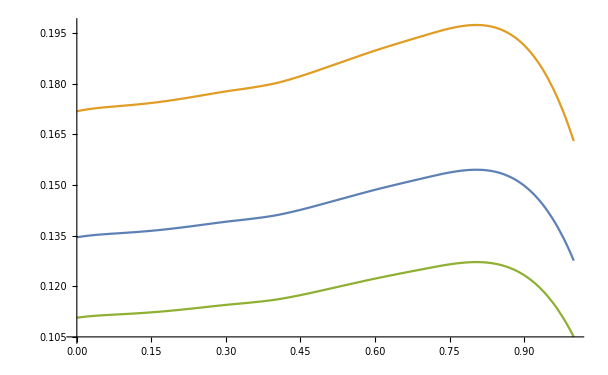

```mathematica
Plot[{gfitbb2inter[x],gfitbb2interu[x],gfitbb2interl[x]},{x,0,1},PlotRange->All]
```

```mathematica
Export["final/data/Upsilon2_width_T250_perp.dat",N[Table[{u,gfitbb2inter[u],gfitbb2interu[u],gfitbb2interl[u]},{u,0,1,1/20}]]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

final/data/Upsilon2_width_T250_perp.dat

```mathematica
NotebookSave[];
```

```mathematica
Transpose[{uscan,wrfitbb[[All,3]]}]
```

{{1/10,10.0476},{1/5,10.0482},{3/10,10.0506},{2/5,10.0277},{1/2,10.0587},{3/5,10.1445},{7/10,10.061},{4/5,10.0572},{9/10,10.045},{99/100,10.0563}}

```mathematica
Transpose[{uscan,gfitbb[[All,3]]}]
```

{{1/10,0.201149},{1/5,0.201164},{3/10,0.203808},{2/5,1.63076},{1/2,0.214881},{3/5,1.34567},{7/10,0.217289},{4/5,1.65693},{9/10,0.208926},{99/100,0.193371}}